```mathematica
Quit[]
```

## Functions and Graph Generators

```mathematica
<<"SpinorHelicity`"
<<"GraphGenerator`"
```

### Independent Spin Structures

```mathematica
Options[IndependentSpinStructres]={"MomentumConservation"->True,"MassSquared"->False};

IndependentSpinStructres[dim_Integer,OptionsPattern[]][list__?((Length[#]==2 && IntegerQ[2*#[[2]]])||(Length[#]==3 && IntegerQ[2*#[[2]]] && IntegerQ[2*#[[3]]] && #[[2]]>=Abs[#[[3]]])&)]:=
Module[
{
massivespins=Table[If[Length[i]==2(*if massless*),0,i[[2]]],{i,{list}}],(*a list of all the spins, for massless particles is zero*)
x= Table[If[Length[i]==2,0,i[[3]]],{i,{list}}], (*a list of all the transversality, for massless particles is zero*)
momenta=dim-Sum[i[[2]],{i,{list}}], (*the number of momenta insertions in the structures*)
n=Length[{list}]
},

If[momenta<0,{}];

massivespins=Tuples[(Range[-#,#,1])&/@massivespins]; (*all the possible transversality combinations for the spins*)
massivespins={(*Abs[*)#-x(*]*),#}&/@massivespins; (*for each transversality configuration gives the difference (not in absolute value, it does distinguish between m and OverTilde[m])*)
massivespins={
Product[If[#[[1,i]]>0,MassUntilde[{list}[[i,1]]]^#[[1,i]],MassTilde[{list}[[i,1]]]^(-#[[1,i]])],{i,n}],(*the masses to compensate the mass dimensions*)
Total@Abs[#[[1]]],(*the total difference*)
Table[If[Length[{list}[[i]]]==2,{list}[[i]],{{list}[[i,1]],{list}[[i,2]],#[[2,i]]}],{i,n}](*if massive, changes the original transversalities in all their possible combinations*)
}&/@massivespins;

massivespins=SortBy[massivespins,#[[1]]&];

massivespins=#[[1]]*UniformMassStructres[dim-#[[2]],"MomentumConservation"->OptionValue["MomentumConservation"]][Sequence@@#[[3]]]&/@massivespins; (*applies the algorithm with uniform mass powers*)

(*ITERATIVE ALGORTHM!*)
If[momenta-2>=0&&OptionValue["MassSquared"], (*if we want to consider terms proportional to M^2*)
x=Table[If[Length[i]==2,Nothing,MassTilde[i[[1]]]MassUntilde[i[[1]]]],{i,{list}}]; (*we consider a SINGLE insertion of M^2 for any massive particle*)
massivespins=(*add the structures to those already found*)
Join[
massivespins,
Times@@@Tuples[{x,Flatten@IndependentSpinStructres[dim-2(*two momentum insertions*),"MomentumConservation"->OptionValue["MomentumConservation"],"MassSquared"->OptionValue["MassSquared"]][list]}] (*all the possible combinations of single M^2 with structures with lower mass dimensions*)
];
];

Return[Flatten@massivespins]

]
```

### Uniform Mass Structures

```mathematica
Options[UniformMassStructres]={"MomentumConservation"->True,"Echos"->False};

UniformMassStructres[dim_Integer,OptionsPattern[]][list__]:=
Module[{labels=Part[#,1]&/@{list},spins=Delete[#,1]&/@{list},angles,squares,structures},

{angles,squares}=
Transpose[(*gives the number of angles and the number of squares for each particle*)
If[Length[#]==1(*if massless*),
{Abs[#[[1]]]-#[[1]],Abs[#[[1]]]+#[[1]]},
{#[[1]]-#[[2]],#[[1]]+#[[2]]}(*the definition of transversality for massive particles*)
]&/@spins
];

If[
TrueQ@OptionValue["MomentumConservation"],(*structures given the possible distributions of momentum insertions*)
structures=(Append[#,0]&/@PermutationsOfPartitions[dim-Total[angles]/2-Total[squares]/2,Length[angles]-1]),(*if we consider structures modulo momentum conservation, we can ignore the momentum of the nth-particle*)
structures=PermutationsOfPartitions[dim-Total[angles]/2-Total[squares]/2,Length[angles]]
];

structures={{angles+#,squares+#},#}&/@structures;(*each momentum add an angle and a square*)

structures=If[Length[#[[1]]]<2(*IsLoopLessDoable returns Nothing if no graph is possible*),Nothing,#]&/@(MapAt[Map[IsLoopLessDoable,#,{1}]&,#,1]&/@structures)(*we check if a loop-less graph can be done for both angles and squares*);

structures=SpinStructures[#,labels,Length/@spins,"MomentumConservation"->OptionValue["MomentumConservation"],"Echos"->OptionValue["Echos"]]&/@structures;

structures=Flatten[structures,1];

Return[(*Flatten@*)structures]

]
```

### Auxiliary functions

#### Spin Structures

```mathematica
Options[SpinStructures]={"MomentumConservation"->True,"Echos"->False,"GraphOnly"->False};

SpinStructures[{{anglestructure_List,squarestructure_List},momenta_List},labels_List,spins_List(*1 or 2 if the corresponding particle is massless or massive, respectively*),OptionsPattern[]]:=
Module[{formfactors,angles,squares},

angles=AllNonIntersectingGraphs[anglestructure];
squares=AllNonIntersectingGraphs[squarestructure];

formfactors=Tuples[{angles,squares}];

If[OptionValue["Echos"], (*Printing intermediate sterps*)
Echo[momenta,"Momenta:"];
Echo[Map[DrawStructure[#,labels]&,formfactors,{1}],"Graphs before momentum conservation:"]; (*Draw all the structures, without distinguishing between free massive spinors and momenta*)
If[MemberQ[spins,2],Echo[FreeSpinorsAndMomenta[#,momenta,labels,spins]&/@formfactors,"Graphs with momenta:"]] (*if there is a massive particle, draw the corresponding graph with free spinors and momenta*)
];

If[
OptionValue["MomentumConservation"],
formfactors=PlanarMomentumConservation[#,momenta,"Echos"->OptionValue["Echos"]]&/@formfactors;

If[momenta[[1]]!=0&&anglestructure[[-1]]!=0&&squarestructure[[-1]]!=0,

squares=Length[spins];
angles=
Flatten[(*flatten permutations*)
Permutations/@Flatten[ (*flatten table and permute each element to give both the subtractions for angles and squares*)
Table[
({Join[PadRight[{i},squares-2],#],Join[PadRight[{i},squares-2],Reverse@#]})&/@(PadRight[#,2]&/@IntegerPartitions[i,2])(*the momentum p_1 is contracted with spinors of (n-1) and n*),
{i,momenta[[1]]}],
1],
1](*this are the possible contractions of momentum p_1 with (n-1) and n*);
angles=({anglestructure,squarestructure}-#)&/@angles(*subtractions of the structures*);
angles=If[MemberQ[Flatten[#],_?(#<0&)],Nothing,#]&/@angles(*eliminating the structures for which the valencies becomes negative*);
angles=Map[IsLoopLessDoable,angles,{2}](*checking if structures are doable*);
angles=If[Length[#]==2(*if structures are possible for both angles and squares*),ExtraGraphs[#,{anglestructure,squarestructure}-#,momenta,labels,spins,squares],Nothing]&/@angles(*ExtraGraphs gives the graphs with compatible valencies and <(n-1)|p_1|n] or <n|p_1|(n-1)] appearing explicitly*);
angles=Flatten[angles,1];

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra momentum conservation:"]
];

angles=IndependentConstrainQ/@angles (*we must exclude the structures which are planar, because they do not correspond to extra constraints*);

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra momentum conservation:"]
];

formfactors=ExtraMomentumConservation[formfactors,Length[Join[angles]]];
];

If[MatchQ[Take[RotateRight[momenta,2],{1,4}],{0,0,0,_?(#!=0&)}]&&MatchQ[Take[RotateRight[spins,2],{1,3}],{2,2,2}],

squares=Length[spins];

angles=
Table[
RotateLeft[#,2]&/@(
PadRight[#,squares]&/@
{{i,i,i,i},{i,i,i,i}}
),
{i,#}
]&@Min[Join[Take[RotateRight[anglestructure],{1,3}],Take[RotateRight[squarestructure],{1,3}],{momenta[[2]]}]];
angles=({anglestructure,squarestructure}-#)&/@angles(*subtractions of the structures*);
angles=If[MemberQ[Flatten[#],_?(#<0&)],Nothing,#]&/@angles(*eliminating the structures for which the valencies becomes negative*);
angles=Map[IsLoopLessDoable,angles,{2}](*checking if structures are doable*);
angles=If[Length[#]==2(*if structures are possible for both angles and squares*),ExtraMassiveGraphs[#,momenta,labels,spins,squares,anglestructure[[1]]-#[[1,1]]],Nothing]&/@angles(*ExtraGraphs gives the graphs with compatible valencies and <(n-1)|p_1|n] or <n|p_1|(n-1)] appearing explicitly*);
angles=Flatten[angles,1](*The ExtraMassivegraphs gives a nested structure*);

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra massive momentum conservation:"]
];

{formfactors,angles}={Complement[formfactors,angles],Complement[angles,formfactors]};

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra massive momentum conservation:"]
];

formfactors=ExtraMassiveMomentumConservation[formfactors,squares,Length[Join[angles]]];
]
];

If[OptionValue["Echos"],
If[¬MatchQ[formfactors,{}],Echo[Map[DrawStructure[#,labels]&,formfactors,{1}],"Graphs:"],Echo["No graph survided."]] (*Draw the graph which survived momentum conservation*)
];

If[¬OptionValue["GraphOnly"],
formfactors=FromMatrixToSpinors[#,momenta,labels,spins,"MomentumConservation"->OptionValue["MomentumConservation"],"Echos"->OptionValue["Echos"]]&/@formfactors;
];

Return[formfactors];
]
```

#### Splitting Free Spinors and Momenta

```mathematica
FreeSpinorsAndMomenta[{adjAngle_,adjSquare_},momenta_List,labels_List,spins_List]:=
Module[{newlabels,types,positions,nonmomenta,newangles,newsquares,n,forbiddenEdges},

newlabels=If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}]; (*if the vertex is massive, we made the label appear (d+1) times, where d is the number of its momentum insertions. If it is massless, it must appear only once*)
positions=FoldPairList[TakeDrop,Range@Length[Flatten@newlabels],Length/@newlabels];(*given {1,...m} where m is the number of particles + the number of massive momentum insertions, it splits this list into sublist each corresponding to free spinor + momenta for massive particles and massless vertex*)
forbiddenEdges=Flatten[
Map[
Subsets[#,{2}]&,
If[Length[#]<2,Nothing(*excluding massless vertices and massive states with no momentum insertions*),#]&/@positions,
{1}
],
1];(*the list of edges which connect a momentum vertex with the corresponding free spinor vertex*)

nonmomenta =Part[#,1]&/@positions;

n=Length[Flatten@newlabels];

newangles=
SparseArray[
MapAt[
ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,(*change the labels with the position of free spinor vertices*)
#,
{1}(*ArrayRules gives {non-zero position -> non-zero value}, and we should act only on the positions*)
]&/@ArrayRules[adjAngle],{n,n}(*the dimension of the array must be specified*)];
newsquares=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjSquare],{n,n}];

Do[
n=i[[-1]];
Do[
{newangles[[Sequence@@#]]--,newangles[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@
Part[
Join[
Sort[Select[#,MatchQ[#,{n,_}]&]],
Sort[Select[#,MatchQ[#,{_,n}]&]]
]&@newangles["NonzeroPositions"],
1];
{newsquares[[Sequence@@#]]--,newsquares[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newsquares["NonzeroPositions"],1],
{j,Delete[i,-1]}
],
{i,Reverse/@positions}
];

{newangles,newsquares}=Planarise[#,forbiddenEdges]&/@{newangles,newsquares};(*checks if the algorithm above did a good job!*)

newlabels=Flatten@newlabels;

DrawStructure[{newangles,newsquares},newlabels]

]
```

```mathematica
Planarise[matrix_,forbiddenEdges_]:=
Module[{x=matrix},
While[
IsGraphNonIntesercting[x]==Nothing,
Print["OPS! If you are not Stefano, please ignore!"];
x=(If[IntersectingQ[#["NonzeroPositions"],forbiddenEdges],Nothing,#]&/@SchoutenCrossing[x]);
x=Part[x,1]
];
Return[x]
]
```

#### Planar Momentum Conservation

```mathematica
Options[PlanarMomentumConservation]={"Echos"->False};

PlanarMomentumConservation[{angles_,squares_},momenta_List,OptionsPattern[]]:=
Module[{nonzeroangles=angles["NonzeroPositions"],nonzerosquares=squares["NonzeroPositions"],forbidden={},n=Length[momenta]},

If[momenta[[-2]]!=0,
AppendTo[forbidden,MemberQ[nonzeroangles,{n-1,n}]||MemberQ[nonzerosquares,{n-1,n}]]
];

If[
momenta[[1]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n}],
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{1,n-1}]
}
];
If[
momenta[[-2]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n-1}]
}
]
]
];

If[If[OptionValue["Echos"],Echo[Or@@Echo[forbidden,"Conditions:"]],Or@@forbidden],Return[Nothing],Return[{angles,squares}]]
]
```

```mathematica
ReinstateFirst[list_List,n_Integer]:=SparseArray[Table[{1,i}->list[[i]],{i,(*2, all of them, (n-1) just the one which are restricted to appear*)n-1,n}],{n,n}]

ExtraGraphs[structures_List,valencies_List,momenta_List,labels_List,spins_List,n_Integer]:=(#+(ReinstateFirst[#,n]&/@valencies (*the angles and squares which are going to be reinstated*)))&/@
SpinStructures[
{
structures,
MapAt[
Min[{structures[[1,-2]],structures[[2,-2]],momenta[[-2]]}],
MapAt[
(#-valencies[[1,1]])&,
momenta,
{1}
],
{-2}
]
},
labels,
spins,
"GraphOnly"->True];

IndependentConstrainQ[{angles_SparseArray,squares_SparseArray}]:=If[MatchQ[IsGraphNonIntesercting[angles],Nothing]||MatchQ[IsGraphNonIntesercting[squares],Nothing],{angles,squares},Nothing]

ExtraMomentumConservation[formfactors_List,n_Integer]:=DeleteCases[formfactors,_?(ExtraConditions[#]&),1,n]

ExtraConditions[formfactor_List]:=(formfactor[[1,-2,-1]]!=0&&formfactor[[2,1,-1]]!=0)||(formfactor[[2,-2,-1]]!=0&&formfactor[[1,1,-1]]!=0)||(formfactor[[1,1,-1]]!=0&&formfactor[[2,1,-1]]!=0)
```

```mathematica
ReinstateMassive[m_Integer,n_Integer]:={SparseArray[{{1,n}->m,{2,n-1}->m},{n,n}],SparseArray[{{n-1,n}->m,{1,2}->m},{n,n}]}

ExtraMassiveGraphs[structures_List,momenta_List,labels_List,spins_List,n_Integer,m_Integer(*the number of "factorised" structures*)]:=(#+(ReinstateMassive[m,n] (*the angles and squares which are going to be reinstated (the "factorised" structure)*)))&/@SpinStructures[{structures,MapAt[(#-m)&,momenta,{2}](*we subtract the number of momenta p_2, in the "factorised" structure <1 n>^m [(n-1) n]^m <(n-1)|p_2|n]^m*)},labels,spins,"GraphOnly"->True];

ExtraMassiveMomentumConservation[formfactors_List,m_Integer(*number of particles*),n_Integer]:=DeleteCases[formfactors,_?(ExtraMassiveConditions[#,m]&),1,n]

ExtraMassiveConditions[formfactor_List,m_Integer]:=
formfactor[[1,1,m]]!=0&&formfactor[[2,1,2]]!=0&&formfactor[[2,m-1,m]]!=0&&
(
(formfactor[[1,1,m]]!=0&&Sum[formfactor[[1,2,i]],{i,3,m-2}]!=0)(*type 1*)||
(formfactor[[1,1,2]]!=0&&Sum[formfactor[[1,i,m-1]],{i,3,m-2}]!=0)(*type 2*)||
(formfactor[[1,m-1,m]]!=0&&Sum[formfactor[[1,2,i]],{i,3,m-2}]!=0)(*type 3*)||
(formfactor[[1,2,m]]!=0&&Sum[formfactor[[1,i,m-1]],{i,3,m-2}]!=0)(*type 4*)||
(formfactor[[1,1,m]]>1&&Sum[formfactor[[1,2,i]],{i,3,m-2}]!=0&&Sum[formfactor[[1,i,m-1]],{i,3,m-2}]!=0)(*type 5*)||
(formfactor[[1,m-1,m]]!=0&&formfactor[[1,1,2]]!=0&&Sum[formfactor[[1,i,j]],{i,3,m-3},{j,i+1,m-2}]!=0) (*type 6*)
)
```

#### From Matrix to Spinors structures

```mathematica
Options[FromMatrixToSpinors]={"MomentumConservation"->True,"Echos"->True};

FromMatrixToSpinors[{adjAngle_,adjSquare_},momenta_List,labels_List,spins_List,OptionsPattern[]]:=
If[MemberQ[spins,2],
Module[{newlabels,types,positions,nonmomenta,newangles,newsquares,n,forbiddenEdges},

(*Echo[{{adjAngle,adjSquare},momenta}];*)

newlabels=If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}];
positions=FoldPairList[TakeDrop,Range@Length[Flatten@newlabels],Length/@newlabels];
forbiddenEdges=Flatten[Map[Subsets[#,{2}]&,If[Length[#]<2,Nothing,#]&/@positions,{1}],1];

nonmomenta =(* Table[1+Sum[Length[newlabels[[i]]],{i,1,j-1}],{j,1,Length@momenta}]*)Part[#,1]&/@positions;

(*newlabels=Flatten[newlabels];*)
n=Length[Flatten@newlabels];

newangles=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjAngle],{n,n}];
newsquares=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjSquare],{n,n}];

(*newlabels=Flatten[newlabels];*)
(*Echo[{newangles,newsquares}];*)

Do[
n=i[[-1]];
Do[
{newangles[[Sequence@@#]]--,newangles[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@(*Part[Sort[Select[newangles["NonzeroPositions"],MatchQ[#,{n,_}|{_,n}]&]],1]*)
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newangles["NonzeroPositions"],1];
{newsquares[[Sequence@@#]]--,newsquares[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@(*Part[Sort[Select[newsquares["NonzeroPositions"],MatchQ[#,{n,_}|{_,n}]&]],1]*)
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newsquares["NonzeroPositions"],1],
{j,Delete[i,-1]}
],
{i,Reverse/@positions}
];

{newangles,newsquares}=Planarise[#,forbiddenEdges]&/@{newangles,newsquares};

types=Flatten@Table[If[spins[[i]]==1,1,{2,ConstantArray[3,momenta[[i]]]}],{i,Length@positions}];
newlabels=Flatten@newlabels;

(*If[OptionValue["Echos"],Echo[DrawStructure[{newangles,newsquares},newlabels],"New graph:"]];*)

(*If[
TrueQ@OptionValue["MomentumConservation"],
If[PlanarMomentumConservation[{newangles,newsquares},positions,spins],Return[Nothing]]
];*)

Return[(*{newangles,newsquares}*)
Times@@((AngleB[
If[types[[#[[1,1]]]]==1,SpinorML[newlabels[[#[[1,1]]]]],If[types[[#[[1,1]]]]==2,SpinorMV[][newlabels[[#[[1,1]]]]],SpinorMV[$up][newlabels[[#[[1,1]]]],StringJoin["I",ToString[newlabels[[#[[1,1]]]]],ToString[#[[1,1]]]]]]],
If[types[[#[[1,2]]]]==1,SpinorML[newlabels[[#[[1,2]]]]],If[types[[#[[1,2]]]]==2,SpinorMV[][newlabels[[#[[1,2]]]]],SpinorMV[$up][newlabels[[#[[1,2]]]],StringJoin["I",ToString[newlabels[[#[[1,2]]]]],ToString[#[[1,2]]]]]]]]^#[[2]]
)&/@Delete[ArrayRules[newangles],-1])*
Times@@((SquareB[
If[types[[#[[1,1]]]]==1,SpinorML[newlabels[[#[[1,1]]]]],If[types[[#[[1,1]]]]==2,SpinorMV[][newlabels[[#[[1,1]]]]],SpinorMV[$down][newlabels[[#[[1,1]]]],StringJoin["I",ToString[newlabels[[#[[1,1]]]]],ToString[#[[1,1]]]]]]],
If[types[[#[[1,2]]]]==1,SpinorML[newlabels[[#[[1,2]]]]],If[types[[#[[1,2]]]]==2,SpinorMV[][newlabels[[#[[1,2]]]]],SpinorMV[$down][newlabels[[#[[1,2]]]],StringJoin["I",ToString[newlabels[[#[[1,2]]]]],ToString[#[[1,2]]]]]]]]^#[[2]]
)&/@Delete[ArrayRules[newsquares],-1])
]

]
,

If[
TrueQ@OptionValue["MomentumConservation"],
If[PlanarMomentumConservation[{adjAngle,adjSquare},FoldPairList[TakeDrop,Range@Length[Flatten@#],Length/@#],spins]&@(If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}]),Return[Nothing]]
];

Times@@(AngleB[SpinorML[labels[[#[[1,1]]]]],SpinorML[labels[[#[[1,2]]]]]]^#[[2]]&/@Transpose[{adjAngle["NonzeroPositions"],adjAngle["NonzeroValues"]}])*Times@@(SquareB[SpinorML[labels[[#[[1,1]]]]],SpinorML[labels[[#[[1,2]]]]]]^#[[2]]&/@Transpose[{adjSquare["NonzeroPositions"],adjSquare["NonzeroValues"]}])
]
```

#### Draw Structures

```mathematica
DrawStructure[{adjacencyAngle_,adjacencySquare_},labels_List]:=Show[{DrawAdjacencyGraph[adjacencyAngle,"Colour"->Red],DrawAdjacencyGraph[adjacencySquare,"Colour"->Blue,"Labels"->labels]}]
```

## Examples

```mathematica
UniformMassStructres[14,"MomentumConservation"->True][{a,5,2},{b,5,2},{c,2},{d,-2}]
```

{da^2 db^2 ab ca^2 cb^2 ab^5}

```mathematica
UniformMassStructres[3,"MomentumConservation"->True][{1,1/2},{2,1/2},{3,0},{4,0},{5,0}]
```

{12 12^2,13 12 13,23 12 23,24 12 24,34 12 34,34 14 23}

```mathematica
IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
IndependentSpinStructres[6,"MomentumConservation"->True,"MassSquared"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
Complement[%,%%]
```

{12 (43p_2)^2 12,-41 42 33p_2 31 32,-41 12 43p_2 1 32,-42 12 43p_2 2 31,-42 43p_2 1 31 12,42^2 2 1 31^2,-41 43p_2 2 32 12,41^2 1 2 32^2}

{12 (43p_2)^2 12,-41 42 33p_2 31 32,-41 12 43p_2 1 32,-42 12 43p_2 2 31,-42 43p_2 1 31 12,42^2 2 1 31^2,-41 43p_2 2 32 12,41^2 1 2 32^2,41 42 1 1 31 32,41 42 2 2 31 32}

{41 42 1 1 31 32,41 42 2 2 31 32}

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
```

{12 (43p_2)^2 12,-41 42 33p_2 31 32}

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0},{6,1,0}]//Length
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0},{6,0,0}]//Length
```

300

300

Momenta:  {1,0,0,0,0}

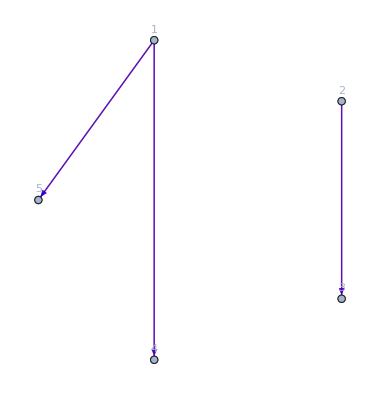
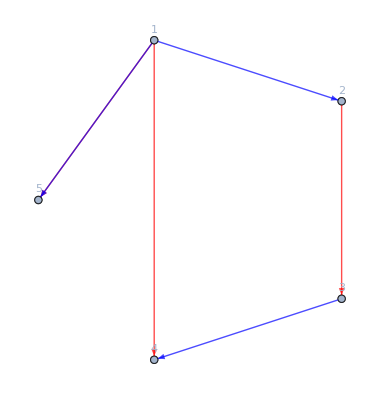
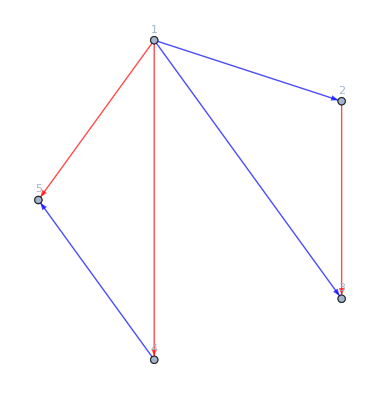
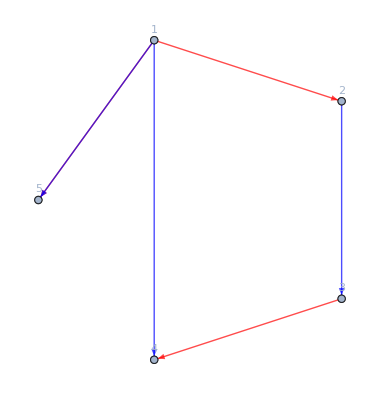
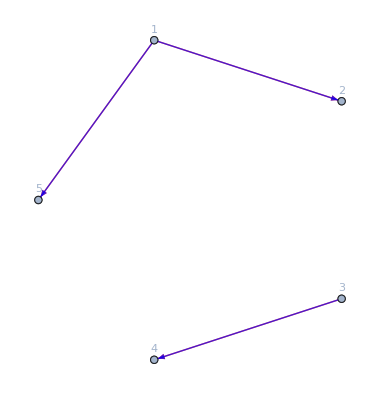
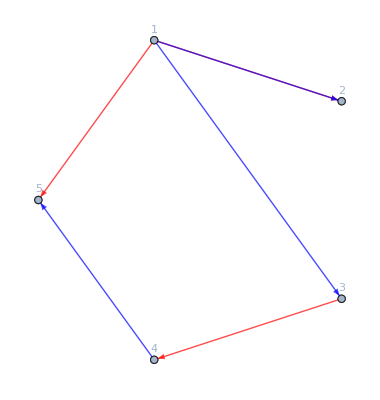
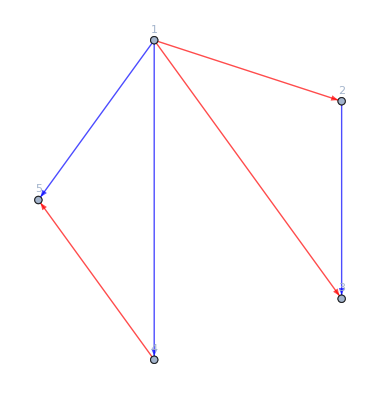
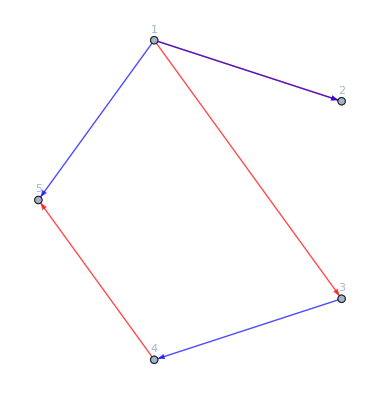
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

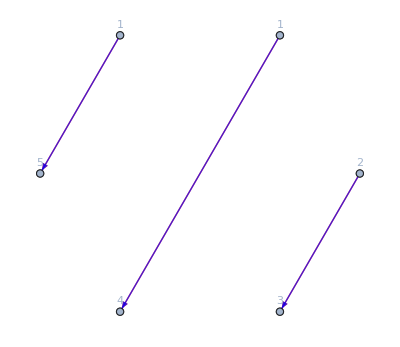
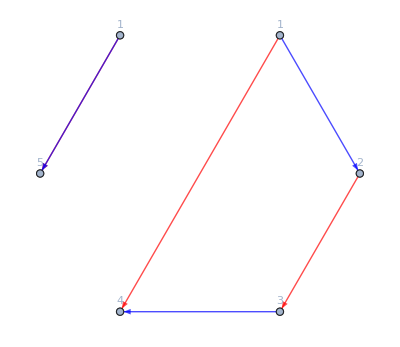
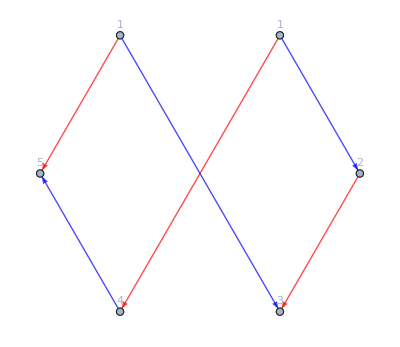
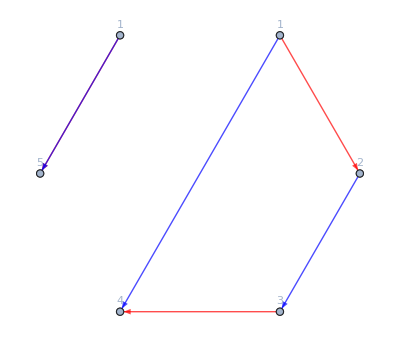
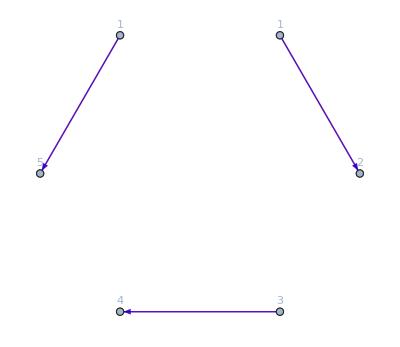
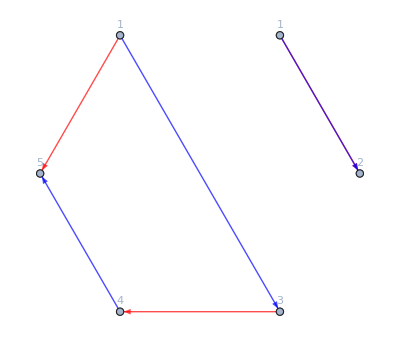
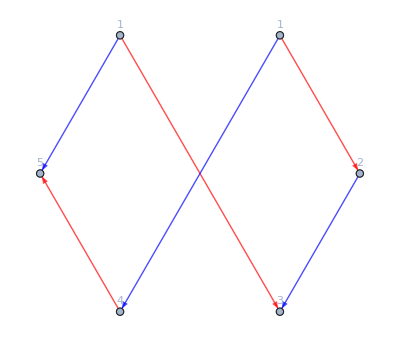
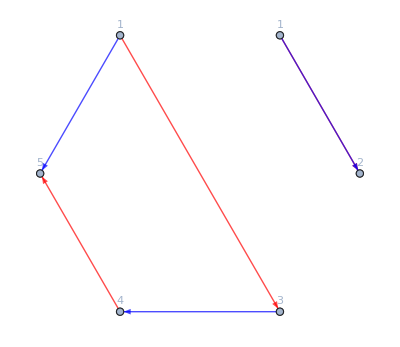
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,True}

True

Conditions:  {True,False}

True

Conditions:  {False,False}

False

Conditions:  {False,True}

True

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

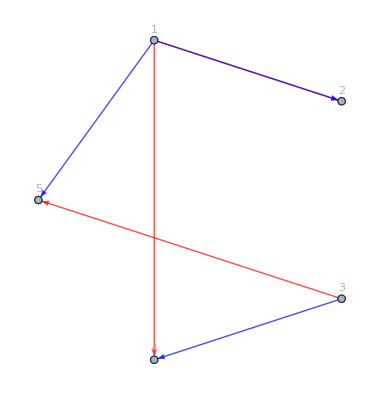
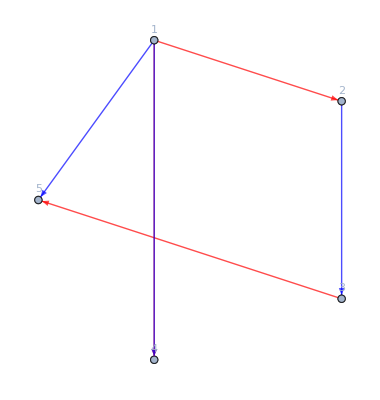
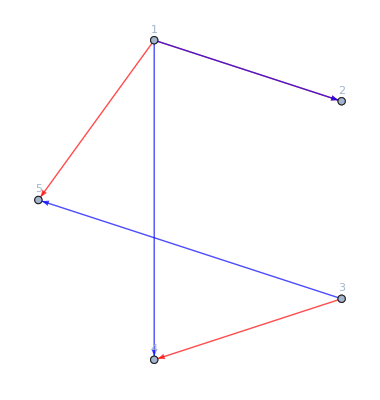
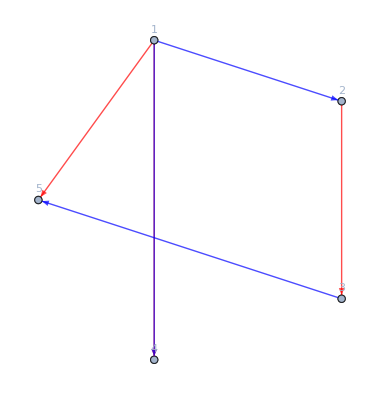
Extra momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,1,0,0,0}

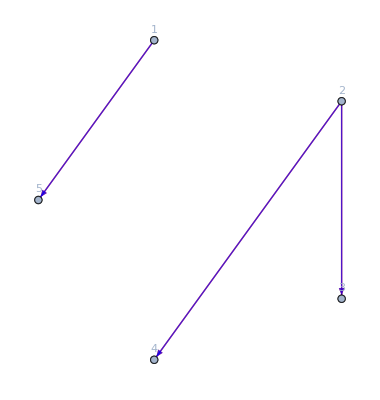
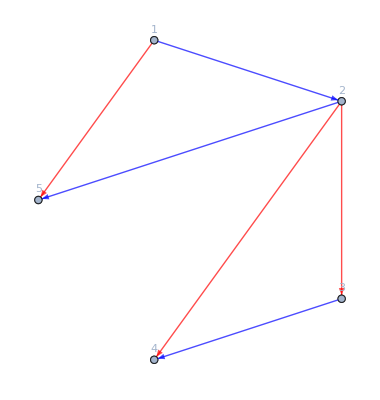
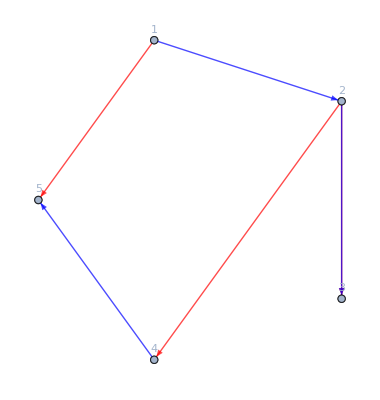
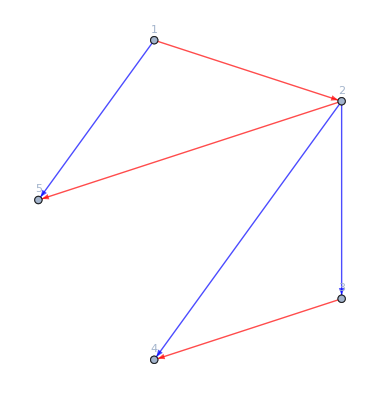
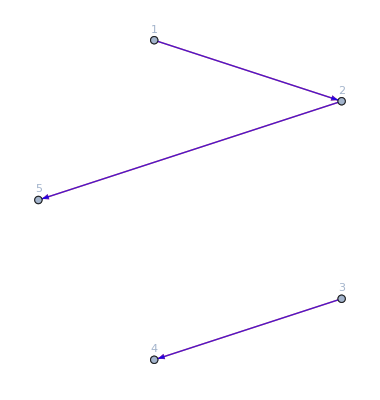
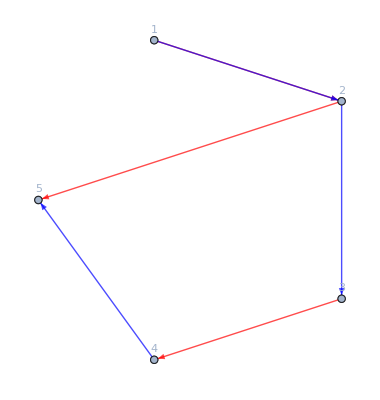
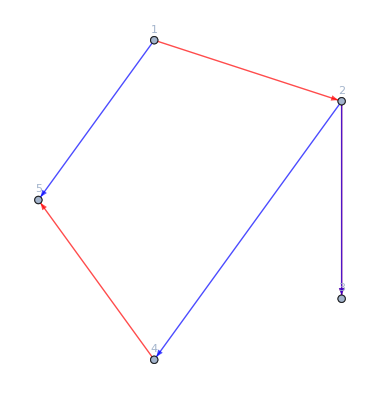
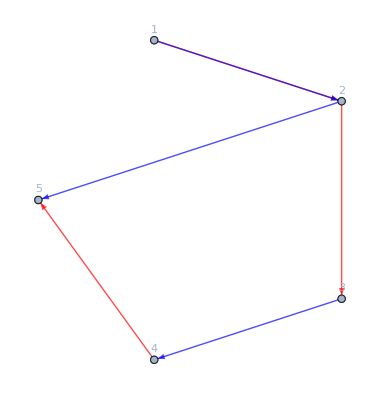
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

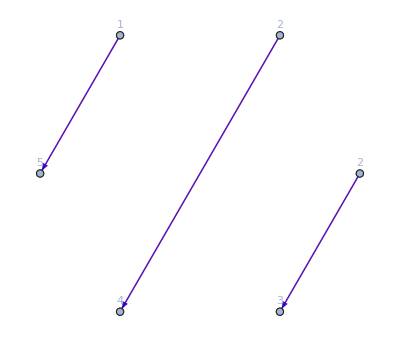
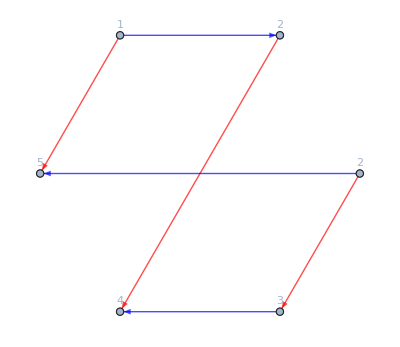
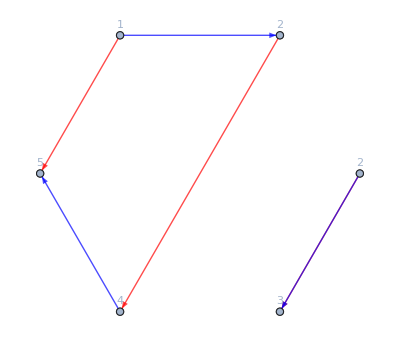
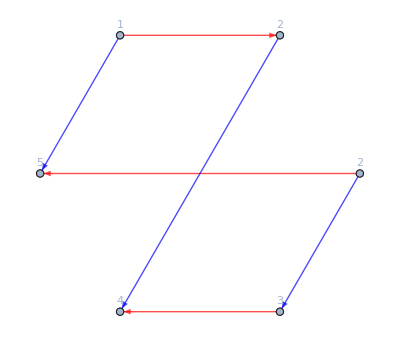
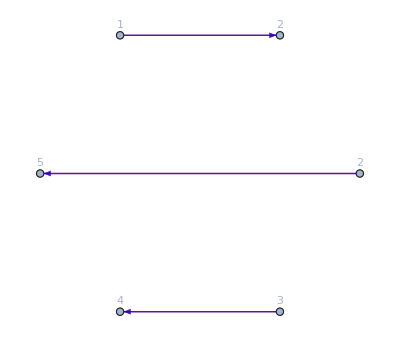
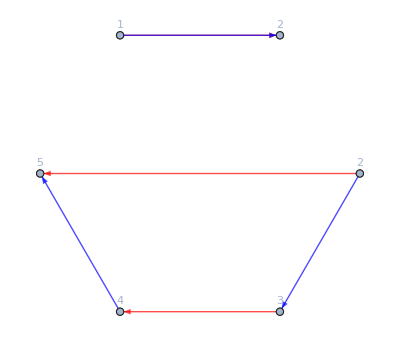
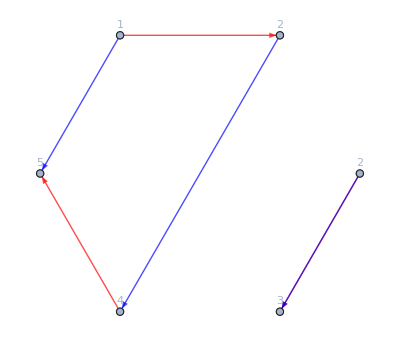
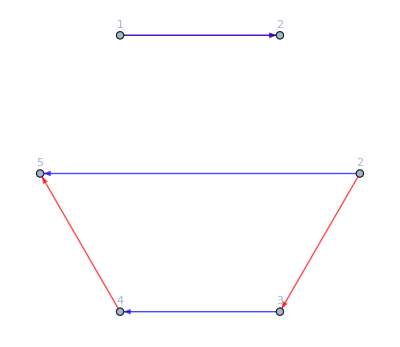
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Extra massive momentum conservation:  {-Graphics-}

Extra massive momentum conservation:  {}

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {0,0,1,0,0}

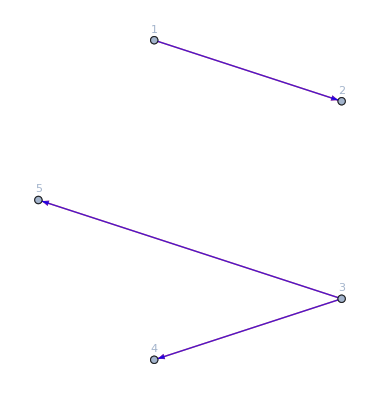
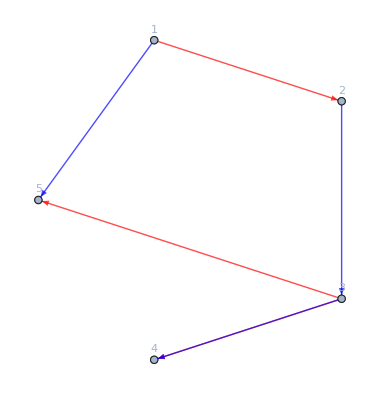
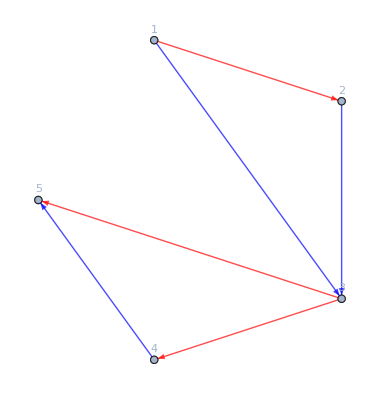
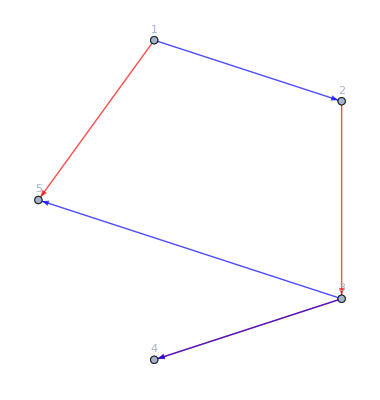
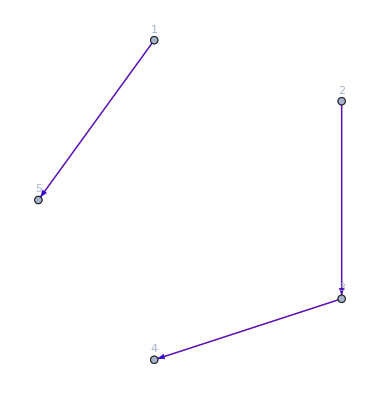
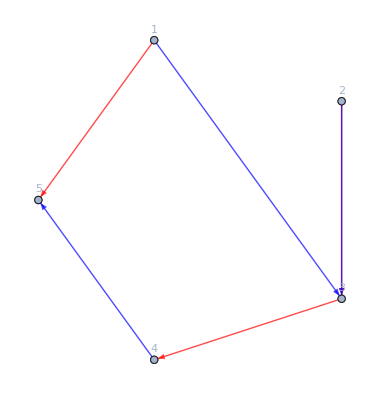
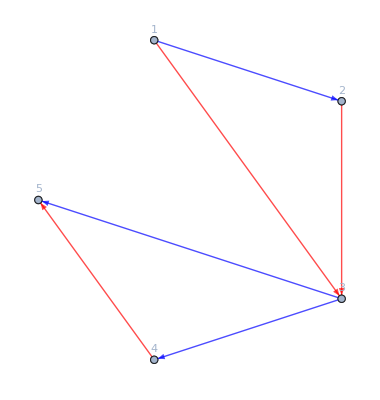
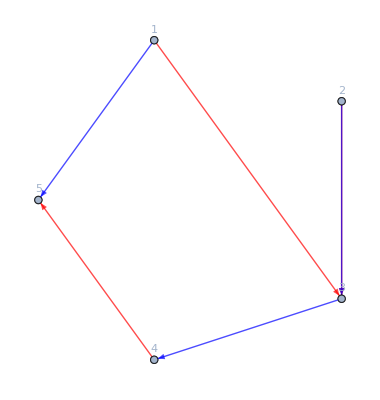
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

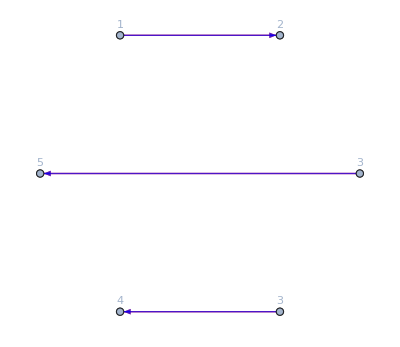
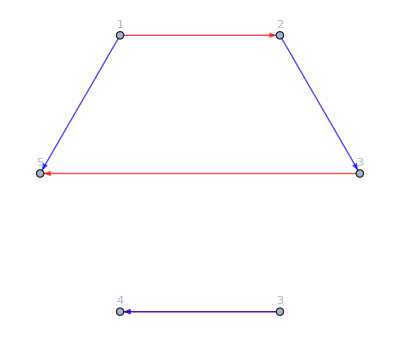
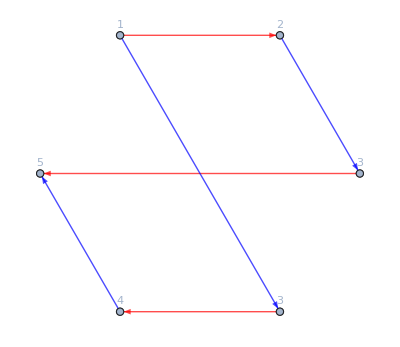
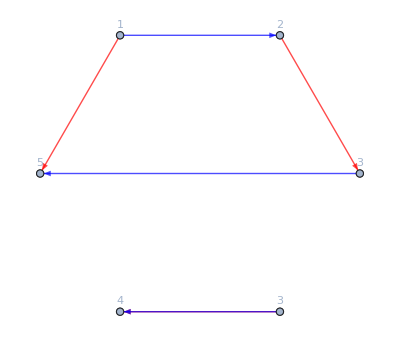
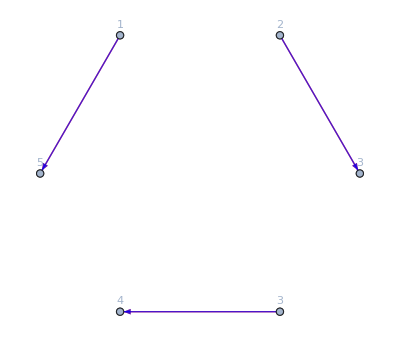
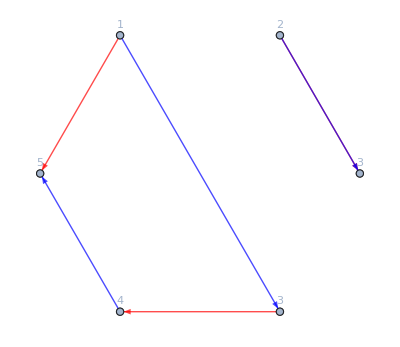
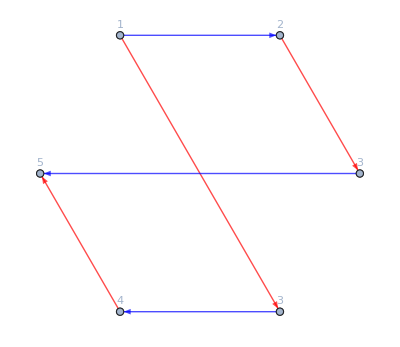
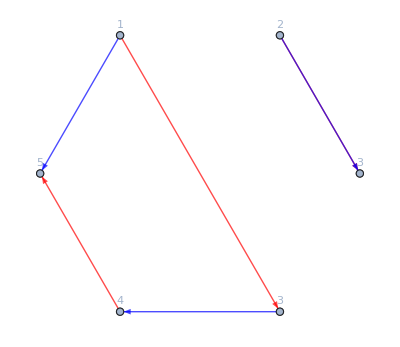
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {0,0,0,1,0}

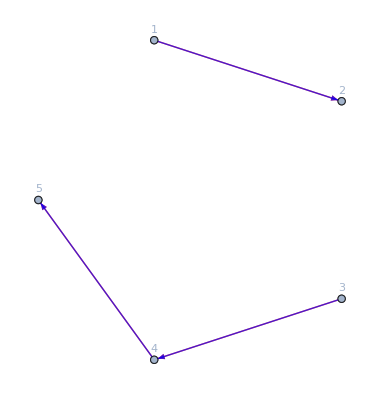
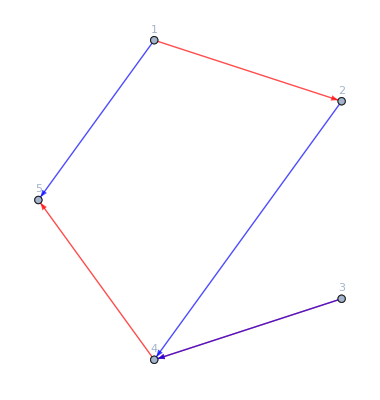
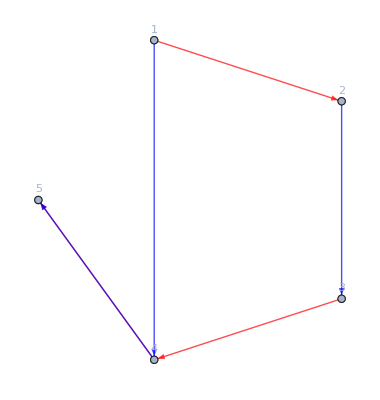
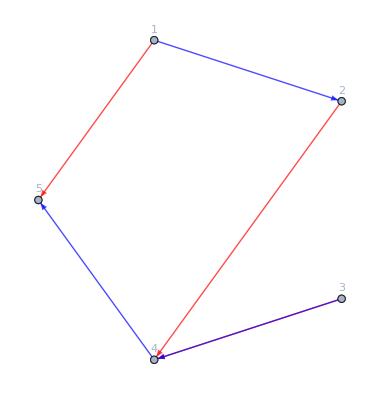
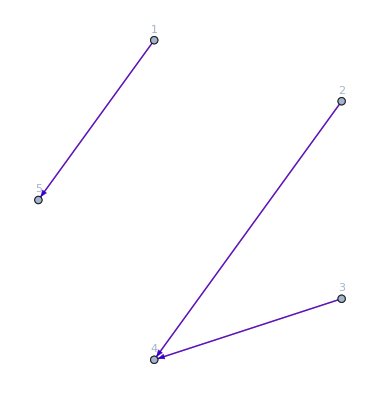
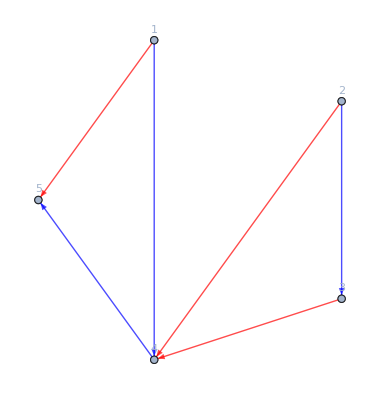
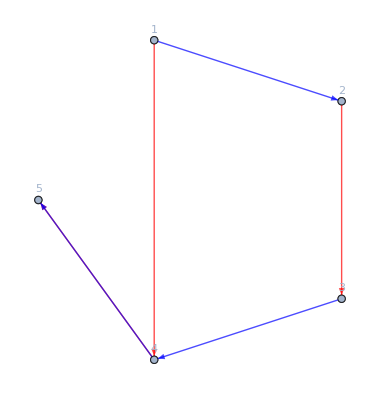
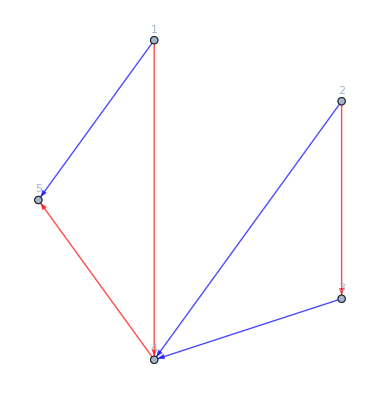
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

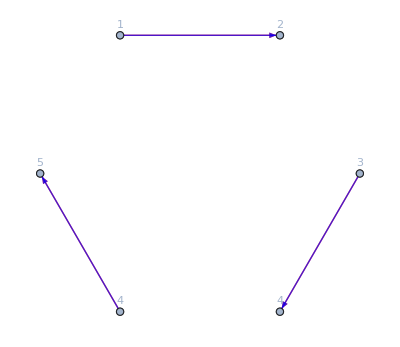
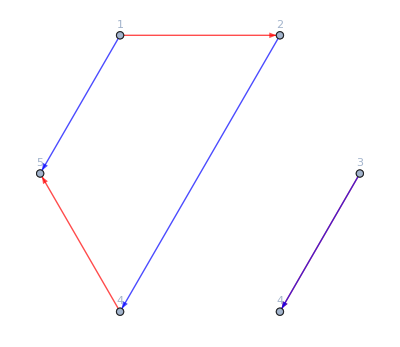
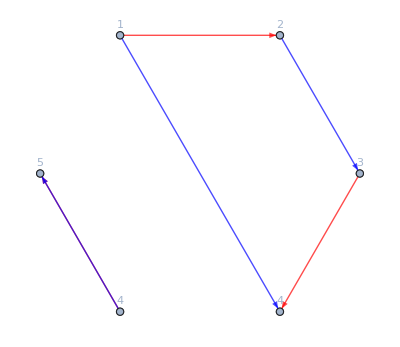
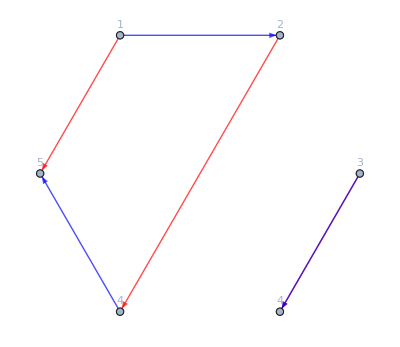
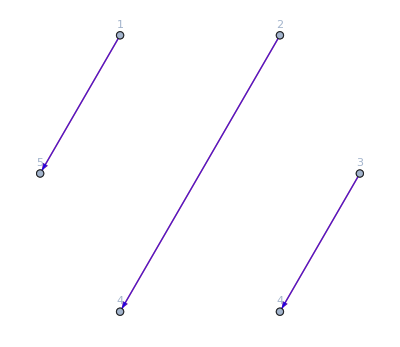
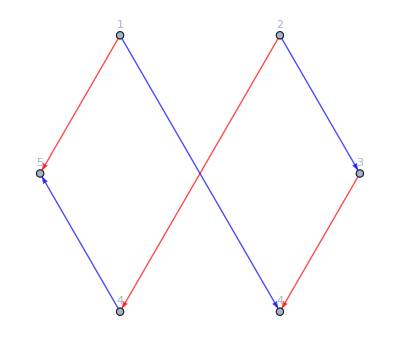
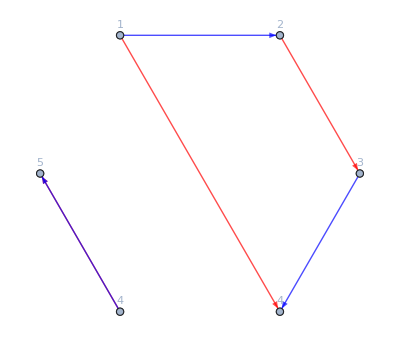
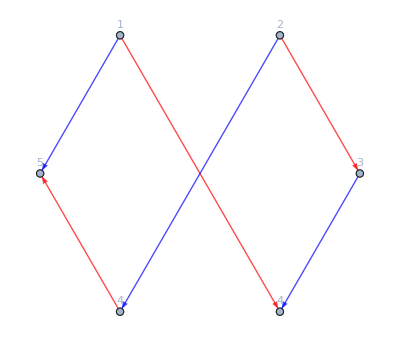
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {False}

False

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Graphs:  {-Graphics-}

{-13 45 22p_1 15 34,-13 45 22p_1 13 45,-12 45 33p_2 12 45,-12 45 35p_2 12 34,-12 45 33p_2 15 24,-12 34 53p_2 12 45,-12 34 55p_2 12 34,-12 34 53p_2 15 24,-15 24 35p_2 12 34,-15 24 33p_2 15 24,-12 35 44p_3 12 35,-12 35 44p_3 15 23,12 35 41p_3 23 45,-15 23 44p_3 12 35,-15 23 44p_3 15 23,15 23 41p_3 23 45,23 45 14p_3 12 35,23 45 14p_3 15 23,-23 45 11p_3 23 45,-15 34 22p_4 15 34}

```mathematica
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}]
```

```mathematica
Length/@(UniformMassStructres[12,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,1,0},{3,1},{4,-1}}]))
(Permutations[{{1,1,0},{2,1,0},{3,1},{4,-1}}]);
{%[[#]],%%[[#]]}&@-9
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

{{{3,1},{2,1,0},{4,-1},{1,1,0}},5}

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1},{2,1,0},{3,-1},{4,1,0}]
```

{-12 31p_2 34p_2 41p_2 12,24 31p_2 33p_2 34p_2 12,-12 34 11p_2 31p_2 12 14}

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
%//Length
```

{-(11p_2)^2 22p_1 34p_2 43,14p_2 11p_2 22p_1 33p_2 41,-12 14p_2 33p_2 41 12 p_2p_3,-12 12p_3 33p_2 41^2 p_2p_3}

4

```mathematica
IndependentSpinStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
```

{-(11p_2)^2 22p_1 34p_2 43,14p_2 11p_2 22p_1 33p_2 41,-12 14p_2 33p_2 41 12 p_2p_3,-12 12p_3 33p_2 41^2 p_2p_3,-12 (14p_2)^2 33p_2 1 12,-13 14p_2 11p_2 22p_1 1 43,-11p_3p_2 12 33p_2 1 41 42,-12 13 14p_2 13p_2 1^2 42,12p_2p_1 12 33p_2 2 41^2,-12p_2p_1 12 31p_2 2 41 43,12^2 33p_2 2 41^2 p_2p_3,-12^2 11p_2 34p_2 1 2 43,12^2 14p_2 33p_2 1 2 41,-12^2 13 14p_2 1^2 2 43,-12 11p_2 (34p_2)^2 3 12,-13p_3p_2 12 34p_2 3 41 12,13p_3p_2 23 12p_3 3 41^2,-12 13 14p_2 34p_2 1 3 12,-13p_3p_2 12 13 1 3 41 42,-12 13^2 14p_2 1^2 3 42,12^2 34p_2 31p_2 2 3 41,-13p_3p_2 12 23 2 3 41^2,12^2 13 34p_2 1 2 3 41,11p_2 22p_1 31p_2 1 41 43,-11p_2 22p_1 33p_2 1 41^2,12 33p_2 1 41^2 12 p_2p_3,-11p_3 22p_3 33p_2 1 41^2,-23p_1p_2 12 2 1 41^2 13,12 21p_3 33p_2 2 1 41^2,12 34p_2 31p_2 3 1 41 12,-13p_3p_2 23 3 1 41^2 12,12 23 31p_2 2 3 1 41^2,-23^2 11p_3 2 3 1 41^2,-22p_1 31p_2 1^2 41^2 13,21p_3 33p_2 1^2 41^2 12,-23 21p_3 2 1^2 41^2 13,23 31p_2 3 1^2 41^2 12,-(14p_2)^2 33p_2 2 12^2,13 14p_2 2 43 12 12p_2p_1,-11p_3p_2 33p_2 2 41 42 12,-(12p_3)^2 33p_2 2 41^2,-13 14p_2 13p_2 1 2 42 12,-13 13p_2 12p_3 1 2 41 42,-13 14p_2 34p_2 3 2 12^2,-13p_3p_2 13 3 2 41 42 12,-13^2 14p_2 1 3 2 42 12,-13^2 12p_3 1 3 2 41 42,-11p_2 34p_2 1 2 43 12^2,14p_2 33p_2 1 2 41 12^2,12p_3 33p_2 1 2 41^2 12,13 34p_2 3 1 2 41 12^2,31p_2 1^2 2 41 43 12^2,-33p_2 1^2 2 41^2 12^2,-(11p_2)^2 22p_1 3 43^2,-(13p_2)^2 22p_1 3 41^2,11p_2 13p_2 22p_1 3 41 43,-12 13p_2 3 41^2 23p_3p_2,12 (13p_2)^2 1 3 41 42,-12 14p_2 13p_2 1 3 43 12,-12 13p_2 23p_1 2 3 41^2,-12p_2p_1 12 2 3 41 43 13,-12^2 11p_2 1 2 3 43^2,12^2 13p_2 1 2 3 41 43,11p_2 22p_1 1 3 41 43 13,-13p_2 22p_1 1 3 41^2 13,-12 1 3 41^2 23 13p_3p_2,-12 23p_1 2 1 3 41^2 13,-22p_1 1^2 3 41^2 13^2,-21p_3 1^2 3 41^2 13 23,-14p_2 13p_2 2 3 43 12^2,(13p_2)^2 2 3 41 42 12,-13p_2 12p_3 2 3 41^2 23,-11p_2 1 2 3 43^2 12^2,13p_2 1 2 3 41^2 12 23,13p_2 1 2 3 41 43 12^2,-11p_3 1 2 3 41^2 23^2,1^2 2 3 41 43 12^2 13,1^2 2 3 41^2 12 13 23}

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{4,1},{3,1,0},{1,2,0},{2,1,0}]//Length
```

4

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
UniformMassStructres[7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]
```

{-12 11p_2 34p_2 43 12,12 14p_2 33p_2 41 12,12 12p_3 33p_2 41^2}

{-24 34p_2 41p_2 12 34,24 33p_2 44p_2 12 14,14 24 31p_2 12 14 34}

```mathematica
IndependentSpinStructres[17,"MomentumConservation"->True][{4,2,0},{3,1,0},{2,1,0},{1,1}]//Length
IndependentSpinStructres[17,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

258

258

```mathematica
list={{1,1},{2,1,0},{3,1,0},{4,2,0}}

massivespins=Table[If[Length[i]==2(*if massless*),0,i[[2]]],{i,list}];(*a list of all the spins, for massless particles is zero*)
x= Table[If[Length[i]==2,0,i[[3]]],{i,list}]; (*a list of all the transversality, for massless particles is zero*)
momenta=9-Sum[i[[2]],{i,list}]; (*the number of momenta insertions in the structures*)
n=Length[list];

massivespins=Tuples[(Range[-#,#,1])&/@massivespins]; (*all the possible transversality combinations for the spins*)
massivespins={Abs[#-x],#}&/@massivespins;(*for each transversality configuration gives the difference (in absolute value, it does not distinguish between m and OverTilde[m])*)
massivespins={
(*Product[Mass[list[[i,1]]]^#[[1,i]],{i,n}],*)(*the masses to compensate the mass dimensions*)
Total@#[[1]],(*the total difference*)
Table[If[Length[list[[i]]]==2,list[[i]],{list[[i,1]],list[[i,2]],#[[2,i]]}],{i,n}](*if massive, changes the original transversalities in all their possible combinations*)
}&/@massivespins
If[Length[UniformMassStructres[9-#[[1]]][Sequence@@#[[2]]]]==Length[UniformMassStructres[9-#[[1]]][Sequence@@Reverse@#[[2]]]],Nothing,#]&/@massivespins
```

{{1,1},{2,1,0},{3,1,0},{4,2,0}}

{{4,{{1,1},{2,1,-1},{3,1,-1},{4,2,-2}}},{3,{{1,1},{2,1,-1},{3,1,-1},{4,2,-1}}},{2,{{1,1},{2,1,-1},{3,1,-1},{4,2,0}}},{3,{{1,1},{2,1,-1},{3,1,-1},{4,2,1}}},{4,{{1,1},{2,1,-1},{3,1,-1},{4,2,2}}},{3,{{1,1},{2,1,-1},{3,1,0},{4,2,-2}}},{2,{{1,1},{2,1,-1},{3,1,0},{4,2,-1}}},{1,{{1,1},{2,1,-1},{3,1,0},{4,2,0}}},{2,{{1,1},{2,1,-1},{3,1,0},{4,2,1}}},{3,{{1,1},{2,1,-1},{3,1,0},{4,2,2}}},{4,{{1,1},{2,1,-1},{3,1,1},{4,2,-2}}},{3,{{1,1},{2,1,-1},{3,1,1},{4,2,-1}}},{2,{{1,1},{2,1,-1},{3,1,1},{4,2,0}}},{3,{{1,1},{2,1,-1},{3,1,1},{4,2,1}}},{4,{{1,1},{2,1,-1},{3,1,1},{4,2,2}}},{3,{{1,1},{2,1,0},{3,1,-1},{4,2,-2}}},{2,{{1,1},{2,1,0},{3,1,-1},{4,2,-1}}},{1,{{1,1},{2,1,0},{3,1,-1},{4,2,0}}},{2,{{1,1},{2,1,0},{3,1,-1},{4,2,1}}},{3,{{1,1},{2,1,0},{3,1,-1},{4,2,2}}},{2,{{1,1},{2,1,0},{3,1,0},{4,2,-2}}},{1,{{1,1},{2,1,0},{3,1,0},{4,2,-1}}},{0,{{1,1},{2,1,0},{3,1,0},{4,2,0}}},{1,{{1,1},{2,1,0},{3,1,0},{4,2,1}}},{2,{{1,1},{2,1,0},{3,1,0},{4,2,2}}},{3,{{1,1},{2,1,0},{3,1,1},{4,2,-2}}},{2,{{1,1},{2,1,0},{3,1,1},{4,2,-1}}},{1,{{1,1},{2,1,0},{3,1,1},{4,2,0}}},{2,{{1,1},{2,1,0},{3,1,1},{4,2,1}}},{3,{{1,1},{2,1,0},{3,1,1},{4,2,2}}},{4,{{1,1},{2,1,1},{3,1,-1},{4,2,-2}}},{3,{{1,1},{2,1,1},{3,1,-1},{4,2,-1}}},{2,{{1,1},{2,1,1},{3,1,-1},{4,2,0}}},{3,{{1,1},{2,1,1},{3,1,-1},{4,2,1}}},{4,{{1,1},{2,1,1},{3,1,-1},{4,2,2}}},{3,{{1,1},{2,1,1},{3,1,0},{4,2,-2}}},{2,{{1,1},{2,1,1},{3,1,0},{4,2,-1}}},{1,{{1,1},{2,1,1},{3,1,0},{4,2,0}}},{2,{{1,1},{2,1,1},{3,1,0},{4,2,1}}},{3,{{1,1},{2,1,1},{3,1,0},{4,2,2}}},{4,{{1,1},{2,1,1},{3,1,1},{4,2,-2}}},{3,{{1,1},{2,1,1},{3,1,1},{4,2,-1}}},{2,{{1,1},{2,1,1},{3,1,1},{4,2,0}}},{3,{{1,1},{2,1,1},{3,1,1},{4,2,1}}},{4,{{1,1},{2,1,1},{3,1,1},{4,2,2}}}}

{}

```mathematica
UniformMassStructres[8][{1,1},{2,1,0},{3,1,-1},{4,2,0}]//Length
UniformMassStructres[8][Sequence@@Reverse@{{1,1},{2,1,0},{3,1,-1},{4,2,0}}]//Length
```

3

3

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]//Length
UniformMassStructres[9,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

4

4

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,2,0},{2,1,1},{3,1,0},{4,1}]//Length
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,1},{3,1,0},{4,2,0}]//Length
```

3

3

```mathematica
UniformMassStructres[7,"MomentumConservation"->True(*,"Echos"->True*)][{1,2,0},{2,1,0},{3,1,0},{4,1}]//Length
UniformMassStructres[7,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

3

3

```mathematica
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,1},{3,1,0},{4,2,2}]
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,2,2},{2,1,1},{3,1,0},{4,1}]
```

{-33p_2 14^2 24^2,-34p_2 12 14 24 34}

{31p_2 41 43 12^2,-33p_2 41^2 12^2}

```mathematica
Length/@(UniformMassStructres[9,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,0},{2,1,0},{3,1,0},{4,1}}]))
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
UniformMassStructres[11,"MomentumConservation"->True][{1,2,0},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[11,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,0}]//Length
```

5

5

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1},{3,1,0},{4,1}]//Length
UniformMassStructres[10,"MomentumConservation"->True(*,"Echos"->True*)][{1,1,0},{2,1},{3,1},{4,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1},{3,1,0},{4,1,0}]//Length
```

5

5

5

```mathematica
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==56,#,Nothing]&/@Permutations[{{1,2,0},{2,1},{3,1,0},{4,1},{5,2}}]
```

{}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,1},{3,2},{4,2,0},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,2},{4,1},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,1,0},{4,1},{5,2}]//Length
```

47

47

47

```mathematica
UniformMassStructres[12,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[12,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,1,0},{4,2,0}]//Length
```

7

7

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{3,2,0},{2,1,0},{4,2,0}]//Length
```

5

5

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True][{2,0,0},{3,2,0},{1,1,0},{4,2,0}]//Length
```

3

3

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,2,0},{3,2,0},{4,0}}]))
```

{6,6,6,6,10,10,6,6,6,6,10,9,6,6,6,6,10,9,6,6,6,6,6,6}

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,0,0},{3,2,0},{4,2,0}}]))
```

{10,10,6,6,6,6,6,6,6,6,6,6,6,6,10,9,6,6,6,6,10,9,6,6}

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,1,0},{3,2,0},{4,2,0}}]))
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==5,#,Nothing]&/@Permutations[{{1,3,0},{2,1,0},{3,2,0},{4,2,0}}]
```

{10,10,6,7,6,7,6,6,6,5,6,5,6,6,10,9,7,6,6,6,10,9,7,6}

{{{2,1,0},{3,2,0},{4,2,0},{1,3,0}},{{2,1,0},{4,2,0},{3,2,0},{1,3,0}}}

```mathematica
Length/@(UniformMassStructres[6,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,0,0},{3,2,0},{4,2,0}}]))
If[Length[UniformMassStructres[6,"MomentumConservation"->True][Sequence@@#]]==4,#,Nothing]&/@Permutations[{{1,1,0},{2,0,0},{3,2,0},{4,2,0}}]
```

{4,4,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,4,4,3,3}

{{{1,1,0},{2,0,0},{3,2,0},{4,2,0}},{{1,1,0},{2,0,0},{4,2,0},{3,2,0}},{{3,2,0},{2,0,0},{1,1,0},{4,2,0}},{{3,2,0},{2,0,0},{4,2,0},{1,1,0}},{{4,2,0},{2,0,0},{1,1,0},{3,2,0}},{{4,2,0},{2,0,0},{3,2,0},{1,1,0}}}

```mathematica
IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
```

{-34^2 11p_2 34^2,34^2 13p_2 14 34,14 34 31p_2 34^2,-14 34 33p_2 14 34,13 14 34 1 34^2,13 34^2 3 14 34,14 34^2 4 13 34,34^2 1 13 14 34,14 34 3 13 34^2,13 34 4 14 34^2}

{-34 11p_2 34,34 13p_2 14,14 31p_2 34,-14 33p_2 14,13 14 1 34,13 34 3 14,14 34 4 13,34 1 13 14,14 3 13 34,13 4 14 34}

```mathematica
Length/@(UniformMassStructres[4,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,0,0},{3,1,0},{4,1,0}}]))
```

{4,4,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,4,4,3,3}

3

Momenta:  {1,0,0,0}

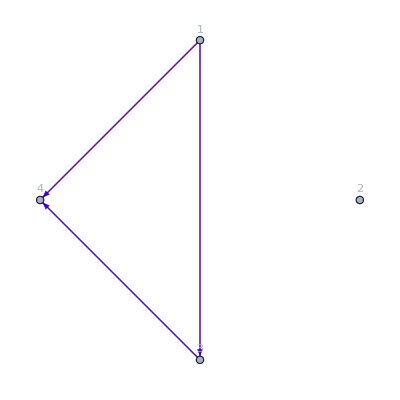
Graphs before momentum conservation:  {-Graphics-}

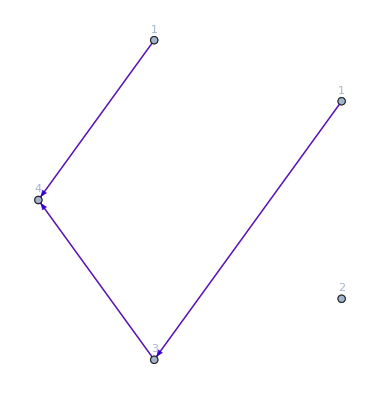
Graphs with momenta:  {-Graphics-}

Conditions:  {True,True}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,0,0}

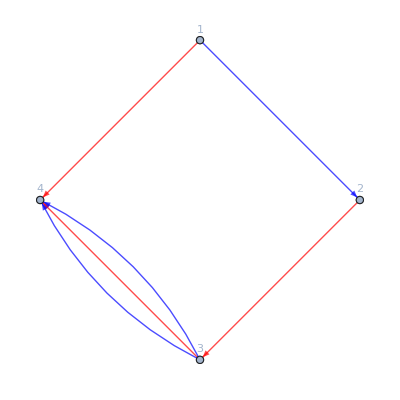
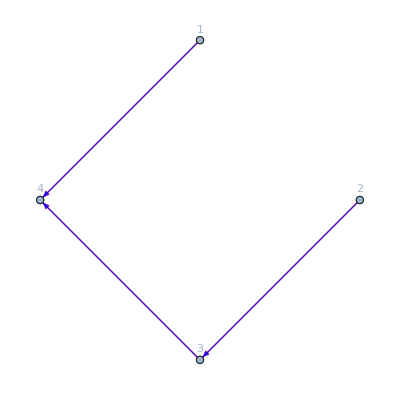
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

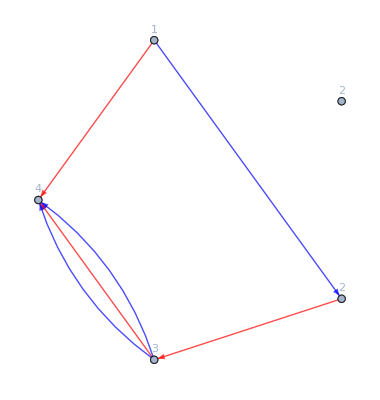
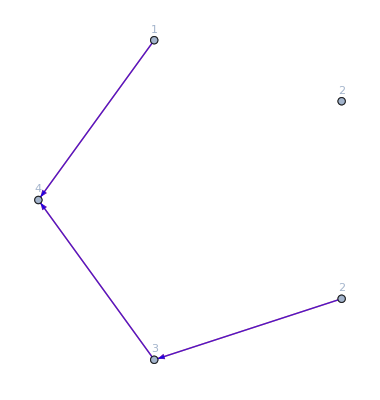
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {0,0,1,0}

Graphs before momentum conservation:  {-Graphics-}

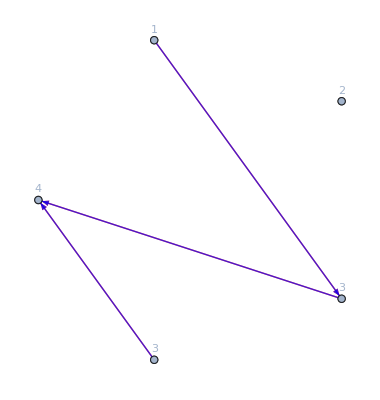
Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

4

Momenta:  {1,0,0,0}

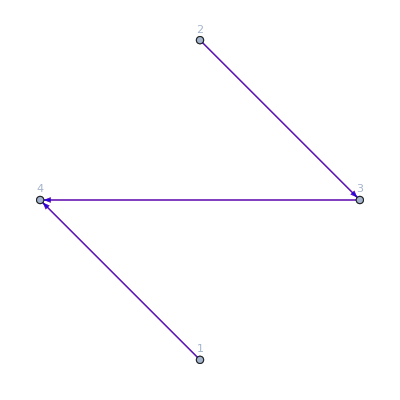
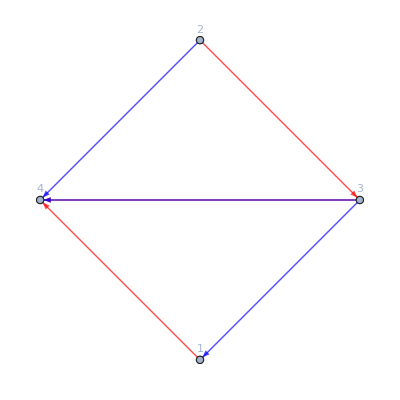
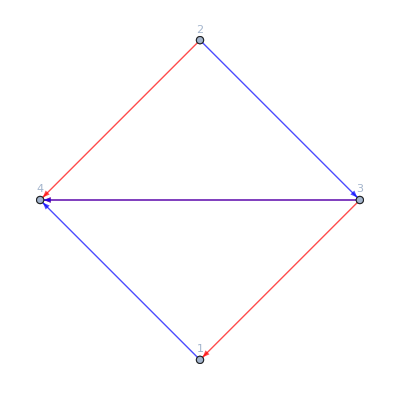
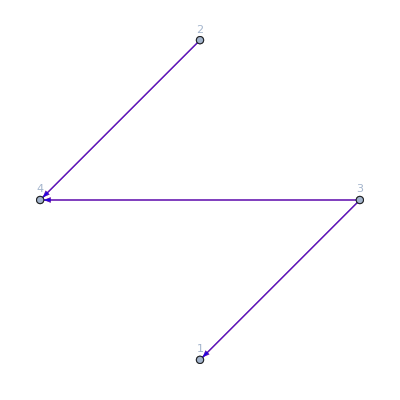
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,1,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {}

False

Graphs:  {-Graphics-}

Momenta:  {0,0,1,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

3

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{3,2,0},{1,1,0},{4,2,0},{2,0,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{2,0,0},{3,2,0},{1,1,0},{4,2,0}]//Length
```

```mathematica
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==10,#,Nothing]&/@Permutations[{{1,1,0},{2,1,0},{3,2,0},{4,2,0}}]
```

{}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,2,0},{2,1},{3,1,0},{4,1},{5,2}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2},{3,1},{4,2,0},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,1,0},{4,1},{5,2}]//Length
```

47

47

47

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,1,0},{a,1,0},{b,2},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,2,0},{3,1,0},{a,1,0},{b,1,0},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,1,0},{3,1,0},{a,2,0},{b,1,0},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,0},{3,1,0},{a,2,0},{b,1,0},{4,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,0},{3,1,0},{a,1,0},{b,1,0},{4,2,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,0},{3,1,0},{a,2},{b,1,0},{4,2,0}]//Length
```

0

240

240

240

«1 more identical outputs»

236

```mathematica
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,2,1},{3,1,0},{4,0}]//Length
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,2,1},{3,0},{4,1,0}]//Length
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,0},{3,2,1},{4,1,0}]//Length
```

6

6

6

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1},{2,1,1},{3,1,0},{4,1,1},{5,1}]//Length
UniformMassStructres[8,"MomentumConservation"->True(*,"Echos"->True*)][{1,1,1},{2,1},{3,1},{4,1,1},{5,1,0}]//Length
```

39

39

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2},{2,1},{3,1},{4,1},{5,1},{6,2},{7,1}]//Length
UniformMassStructres[9,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2},{5,1},{6,1},{7,2}]//Length
```

50

50

```mathematica
Length/@(UniformMassStructres[21,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,1},{2,1,0},{3,1,0},{4,1,0}}]))
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
UniformMassStructres[7,"MomentumConservation"->True,"Echos"->True][{1,2,1},{2,1,0},{3,1,0},{4,1,0}]//Length
UniformMassStructres[7,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,1,0},{3,1,0},{4,2,1}]//Length
```

Momenta:  {0,2,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,True}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-}

No graph survided.

Momenta:  {1,0,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,True,False,True}

True

Conditions:  {False,True,True,True}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {False}

False

Conditions:  {True}

True

Conditions:  {True}

True

Graphs:  {-Graphics-}

3

Momenta:  {2,0,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False}

True

Conditions:  {True,False}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-}

No graph survided.

Momenta:  {0,2,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,2,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,0,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Graphs:  {-Graphics-}

Momenta:  {1,0,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Extra momentum conservatin:  {}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,1,0}

Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

3

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,2,0},{2,1},{3,1},{4,1}]
(*UniformMassStructres[6,"MomentumConservation"->True][{4,2,1},{2,1},{3,1},{1,1}]
UniformMassStructres[5,"MomentumConservation"->True][{4,2,2},{2,1},{3,1},{1,1}]
UniformMassStructres[6,"MomentumConservation"->True][{4,2,-1},{2,1},{3,1},{1,1}]//Length
UniformMassStructres[5,"MomentumConservation"->True][{4,2,-2},{2,1},{3,1},{1,1}]//Length*)
```

{21^2 23 24 21^2 34,21^2 23^2 24 21 41,21 31 23^3 41^2}

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,0}]
(*UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,1}]
UniformMassStructres[5,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,2}]
UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,-1}]//Length
UniformMassStructres[5,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,-2}]//Length*)
```

{24^2 12^2 23 24 34,24^2 12 14 23^2 24,14 24 12^2 14 23 34}

```mathematica
IndependentSpinStructres [7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,0,0}]
```

{-12 11p_2 31p_2 12 13,-21p_3 33p_2 12 p_2p_3,12 33p_2 12 11p_2p_3,-(21p_3)^2 33p_2 2,-12 21p_3 31p_2 2 13,12 (31p_2)^2 3 12,-23p_3p_2 31p_2 3 12,-23 21p_3 31p_2 2 3,-13 11p_2 2 12^2 13,11p_2 33p_2 2 12^2,33p_2 2 12^2 p_2p_3,13 31p_2 3 2 12^2,-12 11p_2 3 12 13^2,21p_3 3 23 13p_3p_2,-12 3 12 13 13p_3p_2,-12 21p_3 2 3 13^2,13p_2 2 3 12^2 13,-2 3 12 23 13p_3p_2}

## Numerical evaluations and extra relations

```mathematica
GenerateKinematics[4,"Masses"->{2,3},"Echos"->True]
TraceChain[{2,3,4,1}]//NEvaluate
-AngleSquareChain[SpinorMV[$up][2,1],{3,4,1},SpinorMV[$up][2,2]]+AngleSquareChain[SpinorMV[$up][2,2],{3,4,1},SpinorMV[$up][2,1]]//NEvaluate
```

{1→{0,5},21→{2,0},22→{2,4},31→{3,4},32→{3,5},4→{1,3},1→{-31/50,-17/50},21→{11/8,-9/8},22→{9/40,3/40},31→{-4/3,-7/12},32→{-1/6,-2/3},4→{6/5,43/20},1→{{0,0},{-31/10,-17/10}},2→{{23/10,-12/5},{11/2,-9/2}},3→{{-7/2,1/4},{-6,-1/4}},4→{{6/5,43/20},{18/5,129/20}}}

629/16

629/16

### Case study: (1^(J=1), 2^(J=0), 3^(J=1), 4^(J=1))^(Δ=4)

```mathematica
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
```

{-34 11p_2 34,34 13p_2 14,14 31p_2 34,-14 33p_2 14,13 14 1 34,13 34 3 14,14 34 4 13,34 1 13 14,14 3 13 34,13 4 14 34}

```mathematica
UniformMassStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
UniformMassStructres[4,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,0,0}]
```

{-34 11p_2 34,34 13p_2 14,-14 33p_2 14}

{-13 22p_1 13,-12 33p_2 12,-23 11p_3 23}

```mathematica
GenerateKinematics[4,"Masses"->{1,2,3,4}]
```

{11→{0,5},12→{4,5},21→{1,2},22→{3,4},31→{2,1},32→{4,1},41→{5,5},42→{5,3},11→{-37/60,-1/3},12→{73/500,-2/25},21→{1/10,11/10},22→{-1/6,7/6},31→{-41/30,7/15},32→{-31/10,7/5},41→{-1/25,0},42→{-22/75,-2/75},1→{{-37/15,-4/3},{-286/75,-19/15}},2→{{7/15,32/15},{11/15,31/15}},3→{{11/15,-14/15},{26/15,-14/15}},4→{{19/15,2/15},{101/75,2/15}}}

```mathematica
AngleSquareChain[SpinorMV[$up][1,1],{2},SpinorMV[$up][2,1]]
%//NEvaluate
MassTilde[2]*AngleB[SpinorMV[$up][1,1],SpinorMV[$up][2,1]]
%//NEvaluate
```

1121p_2

-35/32

1121 2

-35/32

```mathematica
GenerateKinematics[4,"Masses"->{1,2,3,4}]
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
sum=Sum[%[[i]]*a[i],{i,Length@%}]
SpinorComponents[%]//NEvaluate;
sum/.Flatten@Solve[%==0]
%/.a[2]->1
```

{11→{4,1},12→{2,5},21→{0,2},22→{3,0},31→{5,2},32→{3,2},41→{4,4},42→{3,4},11→{35/36,-11/36},12→{17/234,17/117},21→{-16/9,0},22→{67/24,-7/8},31→{-7/4,1/2},32→{-7/6,-1/4},41→{-59/52,-1/52},42→{-13/8,3/8},1→{{43/26,-31/26},{249/52,-87/52}},2→{{-16/3,0},{-67/12,7/4}},3→{{7/12,11/4},{-7/6,3/2}},4→{{161/52,-81/52},{51/26,-41/26}}}

{-34 11p_2 34,34 13p_2 14,14 31p_2 34,-14 33p_2 14,13 14 1 34,13 34 3 14,14 34 4 13,34 1 13 14,14 3 13 34,13 4 14 34}

a[7] 14 34 4 13+a[2] 34 13p_2 14-a[4] 14 33p_2 14+a[6] 13 34 3 14+a[8] 34 1 13 14-a[1] 34 11p_2 34+a[3] 14 31p_2 34+a[5] 13 14 1 34+a[9] 14 3 13 34+a[10] 13 4 14 34

a[2] 14 34 4 13+a[2] 34 13p_2 14+a[2] 13 34 3 14-a[2] 34 1 13 14-a[2] 14 31p_2 34+a[2] 13 14 1 34-a[2] 14 3 13 34-a[2] 13 4 14 34

14 34 4 13+34 13p_2 14+13 34 3 14-34 1 13 14-14 31p_2 34+13 14 1 34-14 3 13 34-13 4 14 34

This relation does not depend on the mass of the 2nd state

```mathematica
(*GenerateKinematics[4,"Masses"->{1,3,4}]
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0},{3,1,0},{4,1,0}]
sum=Sum[%[[i]]*a[i],{i,Length@%}]
SpinorComponents[%]//NEvaluate;
sum/.Flatten@Solve[%==0]
%/.a[2]->1*)
```

### Case study:(1^(h=0),2^(J=0),3^(J=1),4^(J=1))^(Δ=4)

```mathematica
UniformMassStructres[4,"MomentumConservation"->True][{1,0},{2,0,0},{3,1,0},{4,1,0}]
UniformMassStructres[4,"MomentumConservation"->True][{1,0},{4,1,0},{3,1,0},{2,0,0}]
```

{33p_2 44p_2,-34 11p_2 34,-14 33p_2 14}

{13 14 13 14,-14 33p_4 14,33p_4 44p_3}

```mathematica
UniformMassStructres[4,"MomentumConservation"->True][Sequence@@#]&/@Permutations[{{1,0},{2,0,0},{3,1,0},{4,1,0}}];
Length/@%
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

### Case study: (1^(J=1), 2^(J=1), 3^(J=1), 4^(J=1))^(Δ=6,8)

```mathematica
429/3^4//N
```

5.2963

```mathematica
struc=IndependentSpinStructres[8,"MomentumConservation"->True,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
n=Length@struc
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
component=Take[#,1]&@SpinorComponents[sum]
Do[
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[component]],
{i,430}
];
Solve[%==0]
sum/.Flatten@%;
DeleteCases[Coefficient[#,Table[a[i],{i,n}]]&/@%,0]
%/.{MassUntilde[_]:>0,MassTilde[_]:>0}
```

{11p_2 22p_1 33p_2 44p_2,-12 33p_2 44p_2 12 p_2p_3,-34 11p_2 22p_1 34 p_1p_2,-14 22p_1 33p_2 14 p_1p_2,-14 22p_3 33p_2 14 p_2p_3,-34 13p_2 14p_2 22p_1 1,14 14p_2 22p_1 33p_2 1,12 14 33p_2 1 24 p_2p_3,-24p_1p_2 12 31p_2 2 34,411,14 23 2 4 2 4 14 23,12 34 3 4 3 4 12 34,12 34 3 4 3 4 14 23,14 23 3 4 3 4 12 34,14 23 3 4 3 4 14 23,12 34 4^2 4^2 12 34,12 34 4^2 4^2 14 23,14 23 4^2 4^2 12 34,14 23 4^2 4^2 14 23}
 |  |  |  |

429

{a[1] 1212p_2 2222p_1 3232p_2 4242p_2-a[6] 3242 1232p_2 1242p_2 2222p_1 1+a[7] 1242 1242p_2 2222p_1 3232p_2 1+a[14] 1222 1242 2242p_1 3232p_2 1 2+a[12] 1222^2 3232p_2 4242p_2 1 2-a[16] 3242 1212p_2 2222p_1 3242p_2 3+544+a[11] 1222 2242 3232p_2 2 1242 p_2p_3+a[49] 2242 3232p_2 1 1222 1242 p_2p_3+a[8] 1222 1242 3232p_2 1 2242 p_2p_3+a[61] 1242 3232p_2 2 1222 2242 p_2p_3+a[105] 1222 3232p_2 4 1242 2242 p_2p_3}
 |  |  |  |

{11→{2,8},12→{2,4},21→{7,17},22→{2,16},31→{14,3},32→{18,4},41→{11,8},42→{17,8},11→{-193/24,21/8},12→{7/4,41/48},21→{-1179/5668,79/1308},22→{-112/39,1/6},31→{-119/200,-1051/200},32→{-79/109,-740/109},41→{-1/8,-11/48},42→{-47/200,-103/1200},1→{{-235/12,85/24},{-277/6,11/3}},2→{{12875/654,-114/109},{14876/327,-407/218}},3→{{-6139/10900,4969/10900},{-1121/5450,-3559/5450}},4→{{23/50,-1771/600},{22/25,-86/75}}}

{{a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,a[6]→0,a[7]→0,a[8]→0,a[9]→0,a[10]→0,a[11]→0,a[12]→0,a[13]→0,a[14]→0,a[15]→0,a[16]→0,a[17]→0,a[18]→0,a[19]→0,a[20]→0,a[21]→0,a[22]→0,a[23]→0,a[24]→0,a[25]→0,a[26]→0,a[27]→0,a[28]→0,a[29]→0,a[30]→0,a[31]→0,a[32]→0,a[33]→0,a[34]→0,a[35]→0,a[36]→0,a[37]→0,a[38]→0,a[39]→0,a[40]→0,a[41]→0,a[42]→0,a[43]→0,a[44]→0,a[45]→0,a[46]→0,a[47]→0,a[48]→0,a[49]→0,a[50]→0,a[51]→0,a[52]→0,a[53]→0,a[54]→0,a[55]→0,a[56]→0,a[57]→0,a[58]→0,a[59]→0,a[60]→0,a[61]→0,a[62]→0,a[63]→0,a[64]→0,a[65]→0,a[66]→0,a[67]→0,a[68]→0,a[69]→0,a[70]→0,a[71]→0,a[72]→0,a[73]→0,a[74]→0,a[75]→0,a[76]→0,a[77]→0,a[78]→0,a[79]→0,a[80]→0,a[81]→0,a[82]→0,a[83]→0,a[84]→0,a[85]→0,a[86]→0,a[87]→0,a[88]→0,a[89]→0,a[90]→0,a[91]→0,a[92]→0,a[93]→0,a[94]→0,a[95]→0,a[96]→0,a[97]→0,a[98]→0,a[99]→0,a[100]→0,a[101]→0,a[102]→0,a[103]→0,a[104]→0,a[105]→0,a[106]→0,a[107]→0,a[108]→0,a[109]→0,a[110]→0,a[111]→0,a[112]→0,a[113]→0,a[114]→0,a[115]→0,a[116]→0,a[117]→0,a[118]→0,a[119]→0,a[120]→0,a[121]→0,a[122]→0,a[123]→0,a[124]→0,a[125]→0,a[126]→0,a[127]→0,a[128]→0,a[129]→0,a[130]→0,a[131]→0,a[132]→0,a[133]→0,a[134]→0,a[135]→0,a[136]→0,a[137]→0,a[138]→0,a[139]→0,a[140]→0,a[141]→0,a[142]→0,a[143]→0,a[144]→0,a[145]→0,a[146]→0,a[147]→0,a[148]→0,a[149]→0,a[150]→0,a[151]→0,a[152]→0,a[153]→0,a[154]→0,a[155]→0,a[156]→0,a[157]→0,a[158]→0,a[159]→0,a[160]→0,a[161]→0,a[162]→0,a[163]→0,a[164]→0,a[165]→0,a[166]→0,a[167]→0,a[168]→0,a[169]→0,a[170]→0,a[171]→0,a[172]→0,a[173]→0,a[174]→0,a[175]→0,a[176]→0,a[177]→0,a[178]→0,a[179]→0,a[180]→0,a[181]→0,a[182]→0,a[183]→0,a[184]→0,a[185]→0,a[186]→0,a[187]→0,a[188]→0,a[189]→0,a[190]→0,a[191]→0,a[192]→0,a[193]→0,a[194]→0,a[195]→0,a[196]→0,a[197]→0,a[198]→0,a[199]→0,a[200]→0,a[201]→0,a[214]→0,a[215]→0,a[216]→0,a[217]→0,a[218]→0,a[219]→0,a[220]→0,a[221]→0,a[222]→0,a[223]→0,a[224]→0,a[225]→0,a[226]→0,a[227]→0,a[228]→0,a[229]→0,a[230]→0,a[231]→0,a[232]→0,a[233]→0,a[234]→0,a[235]→0,a[236]→0,a[237]→0,a[238]→0,a[239]→0,a[240]→0,a[241]→0,a[242]→0,a[243]→0,a[244]→0,a[245]→0,a[246]→0,a[247]→0,a[248]→0,a[249]→0,a[250]→0,a[251]→0,a[252]→0,a[253]→0,a[254]→0,a[255]→0,a[256]→0,a[257]→0,a[258]→0,a[259]→0,a[260]→0,a[261]→0,a[262]→0,a[263]→0,a[264]→0,a[265]→0,a[266]→0,a[267]→0,a[268]→0,a[269]→0,a[270]→-a[202],a[271]→-a[203],a[272]→-a[204],a[273]→-a[205],a[274]→0,a[275]→0,a[276]→0,a[277]→0,a[286]→0,a[287]→0,a[288]→0,a[289]→0,a[290]→0,a[291]→0,a[292]→0,a[293]→0,a[294]→0,a[295]→0,a[296]→0,a[297]→0,a[298]→0,a[299]→0,a[300]→0,a[301]→0,a[302]→0,a[303]→0,a[304]→0,a[305]→0,a[306]→0,a[307]→0,a[308]→0,a[309]→0,a[310]→0,a[311]→0,a[312]→0,a[313]→0,a[314]→0,a[315]→0,a[316]→0,a[317]→0,a[318]→0,a[319]→0,a[320]→0,a[321]→0,a[322]→0,a[323]→0,a[324]→0,a[325]→0,a[326]→0,a[327]→0,a[328]→0,a[329]→0,a[330]→0,a[331]→0,a[332]→0,a[333]→0,a[334]→0,a[335]→0,a[336]→0,a[337]→0,a[338]→0,a[339]→0,a[340]→0,a[341]→0,a[342]→-a[206],a[343]→-a[207],a[344]→-a[208],a[345]→-a[209],a[346]→-a[278],a[347]→-a[279],a[348]→-a[280],a[349]→-a[281],a[350]→0,a[351]→0,a[352]→0,a[353]→0,a[358]→0,a[359]→0,a[360]→0,a[361]→0,a[362]→0,a[363]→0,a[364]→0,a[365]→0,a[366]→0,a[367]→0,a[368]→0,a[369]→0,a[370]→0,a[371]→0,a[372]→0,a[373]→0,a[374]→0,a[375]→0,a[376]→0,a[377]→0,a[378]→0,a[379]→0,a[380]→0,a[381]→0,a[382]→0,a[383]→0,a[384]→0,a[385]→0,a[386]→0,a[387]→0,a[388]→0,a[389]→0,a[390]→0,a[391]→0,a[392]→0,a[393]→0,a[394]→0,a[395]→0,a[396]→0,a[397]→0,a[398]→0,a[399]→0,a[400]→0,a[401]→0,a[402]→0,a[403]→0,a[404]→0,a[405]→0,a[406]→0,a[407]→0,a[408]→0,a[409]→0,a[410]→0,a[411]→0,a[412]→0,a[413]→0,a[414]→-a[210],a[415]→-a[211],a[416]→-a[212],a[417]→-a[213],a[418]→-a[282],a[419]→-a[283],a[420]→-a[284],a[421]→-a[285],a[422]→-a[354],a[423]→-a[355],a[424]→-a[356],a[425]→-a[357],a[426]→0,a[427]→0,a[428]→0,a[429]→0}}

0

0

```mathematica
DeleteCases[Counts[struc],_?(#==1&)]
```

<|12 34 1 2 1 2 12 34→2,12 34 1 2 1 2 14 23→2,14 23 1 2 1 2 12 34→2,14 23 1 2 1 2 14 23→2,12 34 1 3 1 3 12 34→2,12 34 1 3 1 3 14 23→2,14 23 1 3 1 3 12 34→2,14 23 1 3 1 3 14 23→2,12 34 1 4 1 4 12 34→2,12 34 1 4 1 4 14 23→2,14 23 1 4 1 4 12 34→2,14 23 1 4 1 4 14 23→2,12 34 2 3 2 3 12 34→2,12 34 2 3 2 3 14 23→2,14 23 2 3 2 3 12 34→2,14 23 2 3 2 3 14 23→2,12 34 2 4 2 4 12 34→2,12 34 2 4 2 4 14 23→2,14 23 2 4 2 4 12 34→2,14 23 2 4 2 4 14 23→2,12 34 3 4 3 4 12 34→2,12 34 3 4 3 4 14 23→2,14 23 3 4 3 4 12 34→2,14 23 3 4 3 4 14 23→2|>

```mathematica
IndependentSpinStructres[8,"MomentumConservation"->True,"MassSquared"->False][{1,1,0},{2,1,0},{3,1,0},{4,1,0}];
DeleteCases[Counts[%],_?(#==1&)]
```

<||>

```mathematica
IndependentSpinStructres[8,"MomentumConservation"->True,"MassSquared"->False][{1,1,0},{2,1,0},{3,1,0},{4,1,0}];
IndependentSpinStructres[8,"MomentumConservation"->True,"MassSquared"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0}];
Complement[%,%%];
DeleteCases[Counts[struc],_?(#==1&)]
```

<|12 34 1 2 1 2 12 34→2,12 34 1 2 1 2 14 23→2,14 23 1 2 1 2 12 34→2,14 23 1 2 1 2 14 23→2,12 34 1 3 1 3 12 34→2,12 34 1 3 1 3 14 23→2,14 23 1 3 1 3 12 34→2,14 23 1 3 1 3 14 23→2,12 34 1 4 1 4 12 34→2,12 34 1 4 1 4 14 23→2,14 23 1 4 1 4 12 34→2,14 23 1 4 1 4 14 23→2,12 34 2 3 2 3 12 34→2,12 34 2 3 2 3 14 23→2,14 23 2 3 2 3 12 34→2,14 23 2 3 2 3 14 23→2,12 34 2 4 2 4 12 34→2,12 34 2 4 2 4 14 23→2,14 23 2 4 2 4 12 34→2,14 23 2 4 2 4 14 23→2,12 34 3 4 3 4 12 34→2,12 34 3 4 3 4 14 23→2,14 23 3 4 3 4 12 34→2,14 23 3 4 3 4 14 23→2|>

### Case study: (1^(J=1), 2^(J=1), 3^(J=0), 4^(J=1)(,5^(J=1)))^(Δ=6)

```mathematica
Length/@(IndependentSpinStructres[6,"MomentumConservation"->True][Sequence@@#]&/@Permutations[{{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}}])
```

{124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124,124}

```mathematica
Length@IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}]
Length@IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,0,0},{5,1,0}]
```

124

124

```mathematica
Length@UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}]
Length@UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,0,0},{5,1,0}]
```

65

65

```mathematica
Length@UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}]
Length@UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,0,0},{5,1,0}]
```

137

137

```mathematica
If[FreeQ[#,1|4|5],#,Nothing]&/@UniformMassStructres[2,"MomentumConservation"->True][{1,0,0},{2,1,0},{3,0,0},{4,0,0},{5,0,0}]
If[FreeQ[#,1|4|5],#,Nothing]&/@UniformMassStructres[4,"MomentumConservation"->True][{1,0,0},{2,1,0},{3,0,0},{4,0,0},{5,0,0}]
If[FreeQ[#,1|4|5],#,Nothing]&/@UniformMassStructres[6,"MomentumConservation"->True][{1,0,0},{2,1,0},{3,0,0},{4,0,0},{5,0,0}]
```

{-22p_3}

{22p_3 p_2p_3}

{-22p_3 p_2p_3^2}

```mathematica
struc=IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,0,0},{4,1,0},{5,1,0}]
n=Length@struc;
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
Do[
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"HighestNumber"->20,"Echos"->False];
num=Flatten@Join[num, NEvaluate[SpinorComponents[sum]]],
{i,6}
];
Solve[%==0]
sum/.Flatten@%;
DeleteCases[Coefficient[#,Table[a[i],{i,n}]]&/@%,0]
%/.{MassUntilde[_]:>0,MassTilde[_]:>0}
```

{12 44p_2 55p_2 12,12 44p_3 55p_3 12,-12 44p_3 52p_3 15,12 41p_3 52p_3 45,-15 25p_3 44p_3 12,15 22p_3 44p_3 15,-15 22p_3 41p_3 45,45 14p_3 25p_3 12,-45 14p_3 22p_3 15,45 11p_3 22p_3 45,45 11p_2 22p_1 45,15 22p_1 44p_2 15,-45 14p_3 22p_1 15,45 11p_3 22p_1 45,-15 24 15 24 p_2p_3,15 24 12 45p_3p_2,-15 24 12 45 p_2p_3,45p_3p_2 12 15 24,12 44p_3 55p_2 12,45p_3p_2 12 12 45,-12 45 15 24 p_2p_3,12 45 12 45p_3p_2,-12 45 12 45 p_2p_3,15 22p_4 44p_2 15,15 22p_4 44p_3 15,12 45 14p_2 1 25,-12 15 44p_2 1 25,-14 15 22p_3 1 45,14 15 24p_3 1 25,12 15 42p_3 1 45,-12 15 44p_3 1 25,-12 45 12p_3 1 45,12 45 14p_3 1 25,12 25 41p_2 2 45,-12 25 44p_2 2 15,-15 24 21p_3 2 45,15 24 24p_3 2 15,12 25 41p_3 2 45,-12 25 44p_3 2 15,-12 45 21p_3 2 45,12 45 24p_3 2 15,12^2 45 1 2 45,12 15 24 1 2 45,-15 24 45p_2 4 12,-12 45 45p_2 4 12,-12 45 45p_3 4 12,12 45 42p_3 4 15,-15 24 45p_3 4 12,15 24 42p_3 4 15,14 45 25p_3 4 12,-14 45 22p_3 4 15,12 14 45 1 4 25,14 15 24 1 4 25,15 24^2 2 4 15,12 24 45 2 4 15,-12 45 54p_2 5 12,-15 25 44p_2 5 12,-12 45 54p_3 5 12,12 45 52p_3 5 14,15 45 24p_3 5 12,-15 45 22p_3 5 14,-15 25 44p_3 5 12,15 25 42p_3 5 14,15^2 24 1 5 24,12 15 45 1 5 24,12 25 45 2 5 14,15 24 25 2 5 14,12 45^2 4 5 12,15 24 45 4 5 12,25 41p_2 1 12 45,-25 44p_2 1 12 15,-45 22p_3 1 14 15,45 24p_3 1 12 15,-45 21p_3 1 12 45,25 42p_3 1 14 15,-25 44p_3 1 12 15,25 41p_3 1 12 45,24 25 2 1 14 15,24 45 4 1 12 15,25 45 5 1 12 14,45 14p_2 2 12 25,-15 44p_2 2 12 25,-45 12p_3 2 15 24,45 14p_3 2 12 25,-45 12p_3 2 12 45,15 42p_3 2 15 24,-15 44p_3 2 12 25,15 42p_3 2 12 45,14 15 1 2 24 25,14 45 4 2 12 25,15 45 5 2 12 24,45 1 2 12^2 45,45 1 2 12 15 24,-12 54p_2 4 15 24,-12 54p_2 4 12 45,-12 54p_3 4 12 45,-12 54p_3 4 15 24,12 52p_3 4 14 45,15 24p_3 4 12 45,15 24p_3 4 15 24,-15 22p_3 4 14 45,12 15 1 4 24 45,12 25 2 4 14 45,15 25 5 4 14 24,25 1 4 12 14 45,25 1 4 14 15 24,15 2 4 15 24^2,15 2 4 12 24 45,-12 45p_2 5 12 45,-12 44p_2 5 15 25,-12 45p_3 5 12 45,12 42p_3 5 15 45,-12 44p_3 5 15 25,14 25p_3 5 12 45,-14 22p_3 5 15 45,14 24p_3 5 15 25,12 14 1 5 25 45,12 24 2 5 15 45,14 24 4 5 15 25,24 1 5 15^2 24,24 1 5 12 15 45,14 2 5 12 25 45,14 2 5 15 24 25,12 4 5 12 45^2,12 4 5 15 24 45}

{{a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,a[6]→0,a[8]→0,a[9]→-a[7],a[10]→0,a[11]→0,a[12]→0,a[13]→0,a[14]→0,a[15]→0,a[16]→0,a[17]→a[7],a[18]→0,a[19]→0,a[20]→0,a[21]→-a[7],a[22]→0,a[23]→0,a[24]→0,a[25]→0,a[26]→0,a[27]→0,a[28]→-a[7],a[29]→0,a[30]→0,a[31]→0,a[32]→0,a[33]→0,a[34]→0,a[35]→0,a[36]→-a[7],a[37]→0,a[38]→0,a[39]→0,a[40]→0,a[41]→a[7],a[42]→0,a[43]→0,a[44]→0,a[45]→0,a[46]→0,a[47]→0,a[48]→0,a[49]→0,a[50]→0,a[51]→-a[7],a[52]→0,a[53]→0,a[54]→0,a[55]→0,a[56]→0,a[57]→0,a[58]→0,a[59]→0,a[60]→0,a[61]→-a[7],a[62]→0,a[63]→0,a[64]→0,a[65]→0,a[66]→0,a[67]→0,a[68]→0,a[69]→0,a[70]→0,a[71]→0,a[72]→a[7],a[73]→0,a[74]→0,a[75]→0,a[76]→0,a[77]→0,a[78]→0,a[79]→0,a[80]→0,a[81]→0,a[82]→0,a[83]→a[7],a[84]→0,a[85]→0,a[86]→0,a[87]→0,a[88]→-a[7],a[89]→0,a[90]→0,a[91]→0,a[92]→0,a[93]→0,a[94]→0,a[95]→0,a[96]→0,a[97]→0,a[98]→0,a[99]→0,a[100]→0,a[101]→a[7],a[102]→0,a[103]→0,a[104]→0,a[105]→0,a[106]→0,a[107]→0,a[108]→0,a[109]→0,a[110]→0,a[111]→0,a[112]→0,a[113]→0,a[114]→0,a[115]→a[7],a[116]→0,a[117]→0,a[118]→0,a[119]→0,a[120]→0,a[121]→0,a[122]→0,a[123]→0,a[124]→0,a[125]→0}}

{15 45 22p_3 5 14+45 14p_3 22p_3 15+12 45 24p_3 2 15+14 45 22p_3 4 15-45 22p_3 1 14 15-45 12p_3 2 15 24-15 22p_3 41p_3 45+14 15 22p_3 1 45+15 24 21p_3 2 45-15 42p_3 2 12 45-15 22p_3 4 14 45-14 22p_3 5 15 45+12 45 15 24 p_2p_3-15 24 12 45 p_2p_3}

{45 14p_3 22p_3 15-15 22p_3 41p_3 45+12 45 15 24 p_2p_3-15 24 12 45 p_2p_3}

### Case study: (1^(J=1), 2^(J=2), 3^(J=2), 4^(J=1))^(Δ=8)

```mathematica
struc=IndependentSpinStructres[8,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,2,0},{4,1,0}]
n=Length@struc;
sum=Sum[struc[[i]]*a[i],{i,n}];
num={};
Do[
GenerateKinematics[5,"Masses"->{1,2,3,4,5},"HighestNumber"->20,"Echos"->True];
num=Flatten@Join[num, NEvaluate[SpinorComponents[sum]]],
{i,2}
];
Solve[%==0]
sum/.Flatten@%;
DeleteCases[Coefficient[#,Table[a[i],{i,n}]]&/@%,0]
%/.{MassUntilde[_]:>0,MassTilde[_]:>0}
```

{13 34 (22p_1)^2 13 34,12 24 (33p_2)^2 12 24,12 34 22p_1 33p_2 14 23,12 34 22p_1 33p_2 12 34,14 23 22p_3 33p_2 14 23,-12 13 34 22p_1 1 23 34,-12^2 34 33p_2 1 23 24,-12 14 23 33p_2 1 23 24,-12 23 34 22p_1 2 13 34,-12 23 24 33p_2 2 14 23,-12 23 24 33p_2 2 12 34,12 14 23^2 1 2 23 34,12^2 23 34 1 2 23 34,12 23^2 24 2^2 13 34,-13 23 34 22p_1 3 12 34,-14 23^2 33p_2 3 12 24,-12 23 34 33p_2 3 12 24,13 14 23^2 1 3 23 24,12 13 23 34 1 3 23 24,14 23^3 2 3 12 34,14 23^3 2 3 14 23,12 23^2 34 2 3 12 34,12 23^2 34 2 3 14 23,13 23^2 34 3^2 12 24,-12 34^2 22p_1 4 13 23,-14 23 24 33p_2 4 12 23,-12 24 34 33p_2 4 12 23,12^2 34^2 1 4 23^2,14^2 23^2 1 4 23^2,12 14 23 34 1 4 23^2,14 23^2 24 2 4 13 23,12 23 24 34 2 4 13 23,12 23 34^2 3 4 12 23,14 23^2 34 3 4 12 23,-23 34 22p_1 1 12 13 34,-23 24 33p_2 1 12^2 34,-23 24 33p_2 1 12 14 23,23^2 24 2 1 12 13 34,23^2 24 2 1 13 14 23,23^2 34 3 1 12^2 34,23^2 34 3 1 12 14 23,23 24 34 4 1 12 13 23,-13 34 22p_1 2 12 23 34,-14 23 33p_2 2 12 23 24,-12 34 33p_2 2 12 23 24,12 13 34 1 2 23^2 24,13 14 23 1 2 23^2 24,13 23 34 3 2 12 23 24,12 34^2 4 2 12 23^2,14 23 34 4 2 12 23^2,23 34 1 2 12 14 23^2,23 34 1 2 12^2 23 34,13 34 2^2 12 23^2 24,-12 34 22p_1 3 13 23 34,-12 24 33p_2 3 14 23^2,-12 24 33p_2 3 12 23 34,12^2 34 1 3 23^2 34,12 14 23 1 3 23^2 34,12 23 24 2 3 13 23 34,12 24 34 4 3 13 23^2,14 23 24 4 3 13 23^2,23 24 1 3 13 14 23^2,23 24 1 3 12 13 23 34,12 34 2 3 14 23^3,12 34 2 3 12 23^2 34,14 23 2 3 14 23^3,14 23 2 3 12 23^2 34,12 24 3^2 13 23^2 34,-13 23 22p_1 4 12 34^2,-12 23 33p_2 4 14 23 24,-12 23 33p_2 4 12 24 34,12 13 23 1 4 23 24 34,12 23^2 2 4 12 34^2,12 23^2 2 4 14 23 34,13 23^2 3 4 12 24 34,13 23^2 3 4 14 23 24,23^2 1 4 12^2 34^2,23^2 1 4 14^2 23^2,23^2 1 4 12 14 23 34,13 23 2 4 14 23^2 24,13 23 2 4 12 23 24 34,12 23 3 4 12 23 34^2,12 23 3 4 14 23^2 34}

{11→{3,19},12→{19,19},21→{16,15},22→{10,13},31→{17,3},32→{17,20},41→{0,4},42→{4,18},51→{14,3},52→{16,9},11→{391/1444,-101/1444},12→{265/21052,441/21052},21→{-777/11078,1027/5539},22→{333/1102,-1/551},31→{117/578,-88/289},32→{-565/55199,73/55199},41→{-403/480,497/480},42→{-373/136,851/272},51→{365/3601,-1669/10803},52→{323/3120,-677/3120},1→{{26878/5263,-7325/5263},{25818/5263,-9089/5263}},2→{{-20091/3629,6834/3629},{-19758/3629,8846/3629}},3→{{1381/382,-993/191},{13245/3247,-19787/3247}},4→{{-403/120,497/120},{-5633/1360,8327/1360}},5→{{5731/33240,18811/33240},{13333/22160,-16387/22160}}}

{11→{3,1},12→{19,16},21→{15,9},22→{0,10},31→{14,0},32→{1,6},41→{5,15},42→{11,6},51→{10,7},52→{5,20},11→{214/667,-107/667},12→{615/319,-1784/1595},21→{-1/10,-199/3500},22→{-4/69,119/1725},31→{73/30,-341/420},32→{-1/12,583/5880},41→{-722/2295,-149/2295},42→{134/135,-52/135},51→{-31/165,46/825},52→{-257/561,-403/2805},1→{{79/253,389/1265},{811/253,-1832/1265}},2→{{20/23,-119/115},{-11/23,-383/322}},3→{{18/5,-11/5},{73/5,-341/70}},4→{{-716/85,103/85},{-1426/85,458/85}},5→{{681/187,1604/935},{-103/187,1983/935}}}

{{a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,a[6]→0,a[7]→0,a[8]→0,a[9]→0,a[10]→0,a[11]→0,a[12]→0,a[13]→0,a[14]→0,a[15]→0,a[16]→0,a[17]→0,a[18]→0,a[19]→0,a[20]→0,a[21]→0,a[22]→0,a[23]→0,a[24]→0,a[25]→0,a[26]→0,a[27]→0,a[28]→0,a[29]→0,a[30]→0,a[31]→0,a[32]→0,a[33]→0,a[34]→0,a[35]→0,a[36]→0,a[37]→0,a[38]→0,a[39]→0,a[40]→0,a[41]→0,a[42]→0,a[43]→0,a[44]→0,a[45]→0,a[46]→0,a[47]→0,a[48]→0,a[49]→0,a[50]→0,a[51]→0,a[52]→0,a[53]→0,a[54]→0,a[55]→0,a[56]→0,a[57]→0,a[58]→0,a[59]→0,a[60]→0,a[61]→0,a[62]→0,a[63]→0,a[64]→0,a[65]→0,a[66]→0,a[67]→0,a[68]→0,a[69]→0,a[70]→0,a[71]→0,a[72]→0,a[73]→0,a[74]→0,a[75]→0,a[76]→0,a[77]→0,a[78]→0,a[79]→0,a[80]→0,a[81]→0,a[82]→0,a[83]→0}}

0

0

```mathematica
SpinorComponents[13 34 (22Subscript[p, 1])^2 13 34]
```

{1232 3242 (2222p_1)^2 1232 3242,1232 3242 (2222p_1)^2 1232 3241+1232 3241 (2222p_1)^2 1232 3242,1232 3241 (2222p_1)^2 1232 3241,1232 3242 (2222p_1)^2 1232 3142+1232 3242 (2222p_1)^2 1231 3242+1232 3142 (2222p_1)^2 1232 3242+1231 3242 (2222p_1)^2 1232 3242,218,1131 3142 (2121p_1)^2 1131 3142,1131 3142 (2121p_1)^2 1131 3141+1131 3141 (2121p_1)^2 1131 3142,1131 3141 (2121p_1)^2 1131 3141}
 |  |  |  |

```mathematica
SpinorComponents[sum];//AbsoluteTiming
```

{48.1009,Null}

{47.6615,Null}

```mathematica
UniformMassStructres[4,"MomentumConservation"->True][{1,0,0},{2,2,0},{3,1,0},{4,0,0}]
```

{-23 22p_1 23,-23 22p_3 23}

### Non-linear relations between different structures

```mathematica
GenerateKinematics[4,"Masses"->{2,3,4},"HighestNumber"->10]
IndependentSpinStructres[5,"MomentumConservation"->True][{1,1},{2,0,0},{3,1,0},{4,1,0}]
sum=Sum[%[[i]]*a[i],{i,Echo@Length@%}]
SpinorComponents[%];
Echo@Length[%];
%%//NEvaluate;
sum/.Flatten@Solve[%==0]
```

{1→{1,1},21→{9,6},22→{3,9},31→{9,4},32→{7,3},41→{6,9},42→{10,2},1→{11/3,-53/4},21→{11/207,4/69},22→{7/9,-7/3},31→{23/9,41/15},32→{43/23,49/23},41→{17/78,-87/104},42→{4/351,-47/585},1→{{11/3,-53/4},{11/3,-53/4}},2→{{-472/69,487/23},{-289/69,334/23}},3→{{220/207,-14/345},{13/69,-37/115}},4→{{19/9,-473/60},{1/3,-19/20}}}

{31p_2 41p_2 34,-33p_2 41p_2 14,34 31p_2 3 14,34 41p_2 4 13,41p_2 3 13 34,-43p_2 3 13 14,-33p_2 4 14^2,31p_2 4 14 34,3 4 13 14 34}

9

a[4] 34 41p_2 4 13-a[2] 33p_2 41p_2 14+a[3] 34 31p_2 3 14-a[6] 43p_2 3 13 14-a[7] 33p_2 4 14^2+a[1] 31p_2 41p_2 34+a[5] 41p_2 3 13 34+a[8] 31p_2 4 14 34+a[9] 3 4 13 14 34

9

-a[1] 34 41p_2 4 13+(135 a[1] 33p_2 41p_2 14)/18596-(18731 a[1] 34 31p_2 3 14)/18596+(135 a[1] 43p_2 3 13 14)/18596+(135 a[1] 33p_2 4 14^2)/18596+a[1] 31p_2 41p_2 34+a[1] 41p_2 3 13 34+a[1] 31p_2 4 14 34

```mathematica
GenerateKinematics[4,"Masses"->{1,2,3,4},"HighestNumber"->10]
Det/@Table[NMomentum[i],{i,4}]
IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1,0},{4,1,0}]
Echo[3^4];
sum=Sum[%%[[i]]*a[i],{i,Echo@Length@%%}];
SpinorComponents[%]//NEvaluate;
sum/.Flatten@Solve[%==0];
%/.{a[1]->0,a[2]->0,a[3]->0}
(*Coefficient[#,Table[a[i],{i,56}]]&/@NEvaluate[SpinorComponents[sum]]
RowReduce[%]*)
```

{11→{6,2},12→{10,6},21→{8,2},22→{6,1},31→{4,7},32→{6,0},41→{0,2},42→{4,9},11→{1/28,-11/56},12→{-41/92,-21/184},21→{17/38,-42/19},22→{17/28,-55/28},31→{26/63,-71/126},32→{16/399,71/798},41→{-73/92,59/92},42→{-85/24,71/24},1→{{488/161,-206/161},{178/161,-153/161}},2→{{-289/133,326/133},{-102/133,457/266}},3→{{44/19,-71/19},{-16/57,-71/114}},4→{{-73/23,59/23},{-4/69,-10/69}}}

{-236/161,-493/266,-142/57,14/23}

{12 33p_2 44p_2 12,34 11p_2 22p_1 34,14 22p_1 33p_2 14,14 22p_3 33p_2 14,12 34 13p_2 1 24,-12 14 33p_2 1 24,12 24 31p_2 2 34,-12 24 33p_2 2 14,12^2 34 1 2 34,12 14 23 1 2 34,-14 23 34p_2 3 12,-12 34 34p_2 3 12,12 13 34 1 3 24,13 14 23 1 3 24,14 23^2 2 3 14,12 23 34 2 3 14,-12 34 43p_2 4 12,-14 24 33p_2 4 12,14^2 23 1 4 23,12 14 34 1 4 23,12 24 34 2 4 13,14 23 24 2 4 13,12 34^2 3 4 12,14 23 34 3 4 12,24 31p_2 1 12 34,-24 33p_2 1 12 14,23 24 2 1 13 14,23 34 3 1 12 14,24 34 4 1 12 13,34 13p_2 2 12 24,-14 33p_2 2 12 24,13 14 1 2 23 24,13 34 3 2 12 24,14 34 4 2 12 23,34 1 2 12^2 34,34 1 2 12 14 23,-12 43p_2 3 14 23,-12 43p_2 3 12 34,12 14 1 3 23 34,12 24 2 3 13 34,14 24 4 3 13 23,24 1 3 12 13 34,24 1 3 13 14 23,14 2 3 14 23^2,14 2 3 12 23 34,-12 34p_2 4 12 34,-12 33p_2 4 14 24,12 13 1 4 24 34,12 23 2 4 14 34,13 23 3 4 14 24,23 1 4 14^2 23,23 1 4 12 14 34,13 2 4 12 24 34,13 2 4 14 23 24,12 3 4 12 34^2,12 3 4 14 23 34}

81

56

(10571 a[5] 14 23 34p_2 3 12)/19297-a[5] 12 34 34p_2 3 12+(10571 a[5] 14 24 33p_2 4 12)/19297-a[5] 12 34 43p_2 4 12-a[5] 12 24 34 2 4 13+(10571 a[5] 12 24 33p_2 2 14)/19297-(29868 a[5] 12 23 34 2 3 14)/19297-(10571 a[5] 24 33p_2 1 12 14)/19297-a[5] 14 34 4 2 12 23-(10571 a[5] 12 43p_2 3 14 23)/19297+a[5] 34 1 2 12 14 23+a[5] 12 34 13p_2 1 24+(10571 a[5] 12 14 33p_2 1 24)/19297-a[5] 34 13p_2 2 12 24-(10571 a[5] 14 33p_2 2 12 24)/19297-a[5] 13 34 3 2 12 24-(10571 a[5] 12 33p_2 4 14 24)/19297+a[5] 12 24 31p_2 2 34-a[5] 12 14 23 1 2 34-a[5] 12^2 34 1 2 34-a[5] 24 31p_2 1 12 34+a[5] 12 43p_2 3 12 34+a[5] 12 34p_2 4 12 34+a[5] 34 1 2 12^2 34+a[5] 12 24 2 3 13 34+a[5] 12 23 2 4 14 34+(29868 a[5] 14 2 3 12 23 34)/19297+a[5] 13 2 4 12 24 34